```mathematica
ClearAll["Global`*"];
```

```mathematica
$Version
```

12.3.0 for Mac OS X x86 (64-bit) (May 10, 2021)

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Crossed-polarization (CP) optical microscopy intensity calculation

### A. Input

```mathematica
d=3.5;(*nm, CNC diameter*)
n1=1.33;(*water*)
n3=1.33; (*water*)

(*
Refractive index of cellulose crystal from Reference53: Chae I,et al.Anisotropic Optical and Frictional Properties of Langmuir–Blodgett Film Consisting of Uniaxially-Aligned Rod-Shaped Cellulose Nanocrystals.Advanced Materials Interfaces 7,(2020).
*)
nval=Import["nenodn.xlsx"];
Dimensions[nval]
nval//TableForm

ll=Table[nval[[1,i,1]],{i,2,17}];
nol=Table[nval[[1,i,2]],{i,2,17}];
nel=Table[nval[[1,i,3]],{i,2,17}];
```

{1,17,4}

lamda
no
ne
dn | 250.
1.55726
1.76155
0.20429 | 300.
1.52514
1.7146
0.18946 | 350.
1.50931
1.691
0.18169 | 400.
1.50001
1.67701
0.177 | 450.
1.494
1.66794
0.17394 | 500.
1.48986
1.66168
0.17182 | 550.
1.48688
1.65717
0.17029 | 600.
1.48466
1.6538
0.16914 | 650.
1.48295
1.65122
0.16827 | 700.
1.48161
1.64919
0.16758 | 750.
1.48055
1.64756
0.16701 | 800.
1.47968
1.64625
0.16657 | 850.
1.47896
1.64516
0.1662 | 900.
1.47836
1.64425
0.16589 | 950.
1.47786
1.64349
0.16563 | 1000.
1.47743
1.64284
0.16541

### B. Optical properties

CNC is considered as a thin film
-Graphics-

```mathematica
θ1=N[θ*π/180];(*rad*)

n2p=nel;
n2s=nol;

θ2p=ArcSin[n1 Sin[θ1]/n2p] ; (*Snell's law at the interface between 1 & 2*)
θ3p=ArcSin[n2p Sin[θ2p]/n3] ;(*Snell's law at the interface between 1 & 2*)
θ2s=ArcSin[n1 Sin[θ1]/n2s] ; (*Snell's law at the interface between 1 & 2*)
θ3s=ArcSin[n2s Sin[θ2s]/n3] ;(*Snell's law at the interface between 1 & 2*)

βp=(2 π)/ll d*n2p*Cos[θ2p] ;(* β=(2πd)/λ Subscript[n, 2]*cosθ - Equation 2 *)
βs=(2 π)/ll d*n2s*Cos[θ2s] ;(* β=(2πd)/λ Subscript[n, 2]*cosθ - Equation 2 *)

(*"thin film equations*)
t12p=(2*Cos[θ1]*Sin[θ2p])/(Sin[θ1+θ2p] Cos[θ1-θ2p]);

t12s=(2*Cos[θ1]*Sin[θ2s])/Sin[θ1+θ2s];

t23p=(2*Cos[θ2p]*Sin[θ3p])/(Sin[θ2p+θ3p] Cos[θ2p-θ3p]);

t23s=(2*Cos[θ2s]*Sin[θ3s])/Sin[θ2s+θ3s];

r12p=Tan[θ1-θ2p]/Tan[θ1+θ2p];

r12s=-Sin[θ1-θ2s]/Sin[θ1+θ2s];

r23p=Tan[θ2p-θ3p]/Tan[θ2p+θ3p];

r23s=-Sin[θ2s-θ3s]/Sin[θ2s+θ3s];

t123p=(t12p*t23p Exp[- I*βp])/(1+r12p*r23p Exp[-I*2 βp]);(* Subscript[t, 123]=(Subscript[t, 12]*Subscript[t, 23] Exp[-iβ])/(1+Subscript[r, 12]*Subscript[r, 23] Exp[-i2β]) - Equation 1 *)
t123s=(t12s*t23s Exp[- I*βs])/(1+r12s*r23s Exp[-I*2 βs]);(* Subscript[t, 123]=(Subscript[t, 12]*Subscript[t, 23] Exp[-iβ])/(1+Subscript[r, 12]*Subscript[r, 23] Exp[-i2β]) - Equation 1 *)

T123p=t123p*Conjugate[t123p];
T123s=t123s*Conjugate[t123s];
```

### C. Light properties after passing through a single CNC (add figure) - Electric field, intensity and polarization angle as a function of the polarization angle with respect to the CNC angle

(* Supplementary Figure 8a *)
Ep=E_‖, Es=E_⊥
-Graphics-

```mathematica
(*ϵ= ~0 *)
ϵ=10^-9;
θ=ϵ(*deg*);

(*Incident beam Ep0, Es0, Ip0, Is0*)
Ep0[ϕ_]:=1 Sin[ϕ*(π/180)];
Es0[ϕ_]:=1 Cos[ϕ*(π/180)];
Ip0[ϕ_]:=Ep0[ϕ]^2;
Is0[ϕ_]:=Es0[ϕ]^2;

(* Output beam- Ep1, Es1, Ip1, Is1 after a single CNC *)
Ep[ϕ_]:=Ep0[ϕ]*t123p[[8]];(*[[8]]=600nm *)
Es[ϕ_]:=Es0[ϕ]*t123s[[8]];(*[[8]]=600nm *)
Ip[ϕ_]:=Ep[ϕ]*Conjugate[Ep[ϕ]];
Is[ϕ_]:=Es[ϕ]*Conjugate[Es[ϕ]];

(* Output beam- ψ, (ψ-ϕ) (ϕ dependence) *)
ψ[ϕ_]:=Piecewise[{
{ArcTan[√(Ep[ϕ]*Conjugate[Ep[ϕ]])/√(Es[ϕ]*Conjugate[Es[ϕ]])]*180/π-180,ϕ<-90},
{ArcTan[√(Ep[ϕ]*Conjugate[Ep[ϕ]])/-√(Es[ϕ]*Conjugate[Es[ϕ]])]*180/π+180,ϕ>90},
{ArcTan[√(Ep[ϕ]*Conjugate[Ep[ϕ]])/√(Es[ϕ]*Conjugate[Es[ϕ]])]*180/π,ϕ>0},
{ArcTan[√(Ep[ϕ]*Conjugate[Ep[ϕ]])/-√(Es[ϕ]*Conjugate[Es[ϕ]])]*180/π,ϕ>-90}
}](* ψ=tan^-1[E_‖/E_⊥] - Equation 3 *)

(*Output beam |Etot| and Itot*)
Et[ϕ_]:=√(Ep[ϕ]*Conjugate[Ep[ϕ]]+Es[ϕ]*Conjugate[Es[ϕ]]);(* |Subscript[E, total]|=√(E_‖*E_‖^*+E_⊥*E_⊥^*) - Equation 4 *)
It[ϕ_]:=Et[ϕ]*Conjugate[Et[ϕ]];

(*transmission coefficient*)
tt[ϕ_]:=Et[ϕ]/1;
```

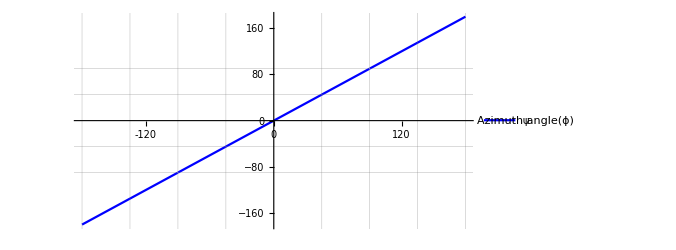
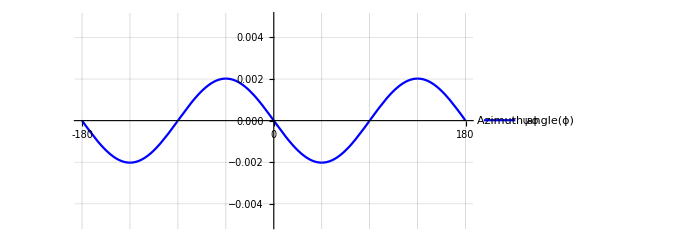

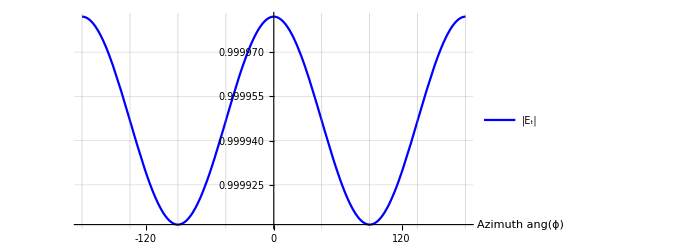
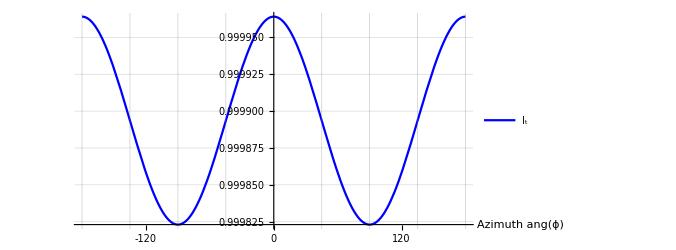

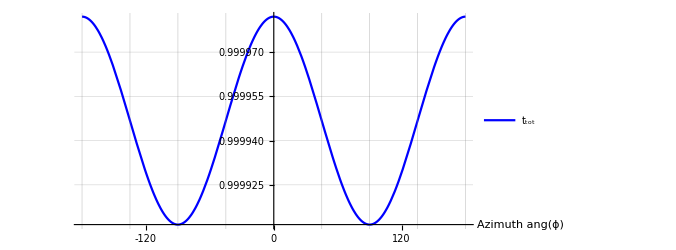

```mathematica
(*check plots*)
{Plot[ψ[ϕ],{ϕ,-180,180},PlotRange->{{-180,180},{-180,180}},Ticks->{Table[30i,{i,-12,12}], Automatic},GridLines->{Table[45i,{i,-4,4}], {-90,-45,45,90}},PlotLegends->Placed[{"ψ"},{0.7,0.9}],PlotStyle->{Blue},AxesLabel->{"Azimuth angle(ϕ)",None},ImageSize->500,AspectRatio->1/2,LabelStyle->{FontFamily->"Arial", FontSize->15,Black}],
Plot[{ψ[ϕ]-ϕ},{ϕ,-180,180},PlotRange->{{-180,180},{-0.005,0.005}},Ticks->{Table[45i,{i,-12,12}], Automatic},GridLines->{Table[45i,{i,-12,12}], Automatic},PlotLegends->Placed[{"ψ-ϕ"},{0.9,0.85}],PlotStyle->{Blue},AxesLabel->{"Azimuth angle(ϕ)",None},ImageSize->500,AspectRatio->1/2,LabelStyle->{FontFamily->"Arial", FontSize->15,Black}](* Supplementary Figure 8b *)
}

{Plot[Et[ϕ],{ϕ,-180,180},PlotRange->{{-180,180},All},Ticks->{Table[30i,{i,-12,12}], Automatic},GridLines->{Table[45i,{i,-12,12}], Automatic},PlotLegends->Placed[{"|E_t|"},{0.84,0.87}],PlotStyle->{Blue},AxesLabel->{"  Azimuth ang(ϕ)",None},ImageSize->500,AspectRatio->1/2,LabelStyle->{FontFamily->"Arial", FontSize->15,Black}](* Supplementary Figure 8c *),
Plot[It[ϕ],{ϕ,-180,180},PlotRange->{{-180,180},All},Ticks->{Table[30i,{i,-12,12}], Automatic},GridLines->{Table[45i,{i,-12,12}], Automatic},PlotLegends->Placed[{"I_t"},{0.84,0.87}],PlotStyle->{Blue},AxesLabel->{"  Azimuth ang(ϕ)",None},ImageSize->500,AspectRatio->1/2,LabelStyle->{FontFamily->"Arial", FontSize->15,Black}]}

Plot[tt[ϕ],{ϕ,-180,180},PlotRange->{{-180,180},All},Ticks->{Table[30i,{i,-12,12}], Automatic},GridLines->{Table[45i,{i,-12,12}], Automatic},PlotLegends->Placed[{"t_tot"},{0.84,0.87}],PlotStyle->{Blue},AxesLabel->{"  Azimuth ang(ϕ)",None},ImageSize->500,AspectRatio->1/2,LabelStyle->{FontFamily->"Arial", FontSize->15,Black}]
```

### D. 100 CNC angle generation for the five CMF organizations: crossed-polylamellate, random, helicoidal (10°), uniaxial, and biomodal.

```mathematica
n=100;(* number of CNCs (layers)*)
ϕ1=60; (* angle of the first CNC*)(*60 deg was chosen as an example - Supplementary Figure 8 *)
ϕ1=ϕ1;(* ϵ is a small number, 10^-9 *)

(*defined functions*)
F360[x_]:=x-Floor[x,360];
F180[x_]:=x-Floor[x,180];
F180off[x_]:=N[ArcSin[Sin[x*π/180]]*180/π];
F90off[x_]:=N[ArcCos[Cos[x*π/180]]*180/π];
```

(* Supplementary Figure 8d *)
Crossed-polylamellate structure as an example
-Graphics-

```mathematica
(* Crossed-polylamellate structure*)
ϕcl=Table[0,{i,1,n}];
ϕcl[[1]]=ϕ1;
dϕcl=Table[0,{i,1,n}];
dϕcl[[1]]=ϕ1;

For[i=1,i<n,i++,
ϕcl[[i+1]]=Round[ϕcl[[i]]+RandomVariate[NormalDistribution[61.9,15.4]]*(-1)^RandomInteger[{1,10}]];
dϕcl[[i+1]]=ϕcl[[i+1]]-ϕcl[[i]];
]

ϕcl;
ϕcl360=F360[ϕcl]
ϕcl180=F180[ϕcl];
ϕcl180Norm=F180[ϕcl180+90];
```

{60,149,229,157,87,27,102,42,323,6,42,333,37,332,293,342,60,129,66,128,61,355,284,214,308,240,190,144,86,83,128,208,141,98,145,212,282,1,83,33,327,236,275,333,36,87,180,239,293,352,40,354,304,224,273,213,258,329,298,12,330,272,211,150,89,40,326,275,341,274,344,59,109,37,330,2,81,38,88,133,72,31,108,52,339,275,332,37,345,33,73,111,170,226,276,198,93,137,98,41}

```mathematica
(* random orientation *)
ϕra=Round[RandomReal[{0,360},n]];
ϕra[[1]]=ϕ1;

dϕra=Table[0,{i,1,n}];
dϕra[[1]]=ϕ1;

For[i=1,i<n,i++,
dϕra[[i+1]]=ϕra[[i+1]]-ϕra[[i]];
]

ϕra;
ϕra360=F360[ϕra]
ϕra180=F180[ϕra];
ϕra180Norm=F180[ϕra180+90];
```

{60,179,348,257,112,39,62,82,341,176,94,19,254,211,53,32,154,251,281,290,157,197,311,235,107,260,318,354,288,40,278,84,121,325,217,147,161,165,278,263,260,72,221,176,86,5,40,136,96,150,112,121,255,159,309,48,159,168,161,209,292,320,45,326,286,341,94,221,280,115,119,163,267,168,162,320,286,272,26,42,36,217,121,289,54,259,105,196,150,182,359,13,192,290,38,122,75,172,0,71}

```mathematica
(* helicoidal 10° *)
ϕhe=Table[0,{i,1,n}];
ϕhe[[1]]=ϕ1;

For[i=1,i<n,i++,
ϕhe[[i+1]]=ϕhe[[i]]+10
]
ϕhe;
ϕhe360=F360[ϕhe]
ϕhe180=F180[ϕhe];
ϕhe180Norm=F180[ϕhe180+90];
```

{60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330}

```mathematica
(* uniaxial 10° *)
ϕun=Round[RandomVariate[NormalDistribution[90,10],n],1]
ϕun;
ϕun360=F360[ϕun];
ϕun180=F180[ϕun];
ϕun180Norm=F180[ϕun180+90];
```

{100,101,84,91,62,86,87,61,92,80,99,92,90,94,81,80,84,72,80,99,82,108,101,88,111,78,85,81,109,101,111,85,94,105,78,82,98,86,87,101,78,99,93,91,79,87,91,97,118,88,84,87,86,90,94,96,81,100,72,97,89,96,86,93,98,84,95,97,95,95,96,91,93,106,75,87,80,94,77,97,108,93,121,108,92,76,81,80,71,100,93,115,108,82,94,77,79,87,80,98}

```mathematica
(* bimodal ° *)
ϕbi=RandomVariate[MixtureDistribution[{1,1},{NormalDistribution[42,8],NormalDistribution[135,10]}],n];
ϕbi=Round[ϕbi,1]
ϕbi360=F360[ϕbi];
ϕbi180=F180[ϕbi];
ϕbi180Norm=F180[ϕbi180+90];
```

{49,140,35,137,39,32,45,136,129,32,36,49,50,125,129,44,128,137,48,49,36,137,43,47,150,51,21,138,128,53,34,53,54,122,137,45,37,39,141,50,47,142,35,134,156,122,121,48,42,140,53,45,116,35,140,135,139,38,35,142,37,134,47,46,165,133,36,48,128,131,148,35,125,144,131,137,29,55,137,48,138,55,137,133,128,146,130,148,46,39,36,143,135,27,51,42,30,33,26,128}

## E. Light properties after the 100 CNC organizations - Loop1 for each organization

```mathematica
ϕi=0;(* the initial polarization direction of the incident beam w.r.t. y-axis *)(*0 deg was chosen as an example - Supplementary Figure 8 *)
ϕi=ϕi+ϵ;(* ϵ is a small number, 10^-9 *)
```

### 1) Cross-polylamellate

#### Storage

```mathematica
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

Etot
ϕcl180

ψy
ϕbtn;
ψres;

dψ;
dψ2;
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{60,149,49,157,87,27,102,42,143,6,42,153,37,152,113,162,60,129,66,128,61,175,104,34,128,60,10,144,86,83,128,28,141,98,145,32,102,1,83,33,147,56,95,153,36,87,0,59,113,172,40,174,124,44,93,33,78,149,118,12,150,92,31,150,89,40,146,95,161,94,164,59,109,37,150,2,81,38,88,133,72,31,108,52,159,95,152,37,165,33,73,111,170,46,96,18,93,137,98,41}

{1.×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Loop

```mathematica
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕcl180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕcl180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)
]
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕ1)*π/180])^2; (* I=(|Subscript[E, total]|*sinψ)^2 - Equation 5 *)
```

#### Check plots and final intensity (Supplementary Figure 8e,f here)

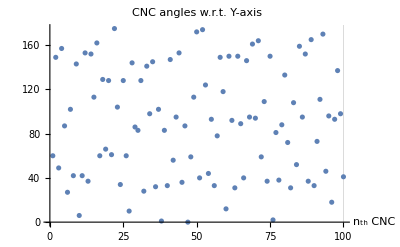
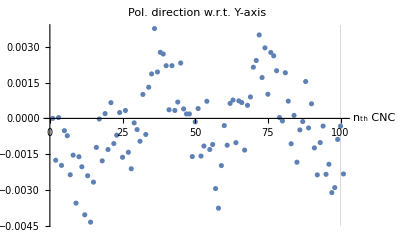
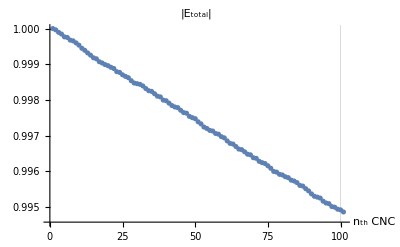
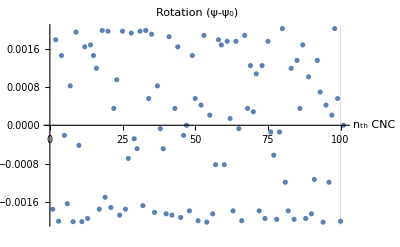

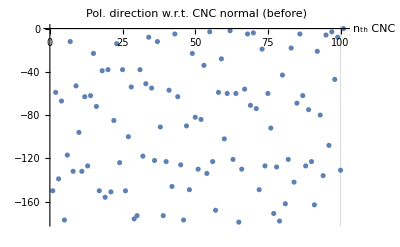
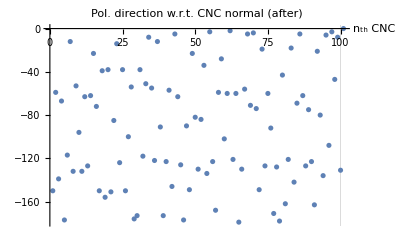

E_total after 100th CNC=0.994861+0. ⅈ

Final intensity after the 2nd polarizer=0.742347+0. ⅈ

```mathematica
{ListPlot[ϕcl180,ImageSize->400,PlotRange->All,AxesLabel->{"n_th CNC",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},GridLines->{{100},{180}},AxesOrigin->{0,0},PlotLabel->"CNC angles w.r.t. Y-axis"](* Supplementary Figure 8e *),
ListPlot[ψy,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. Y-axis",GridLines->{{100},None}](* Supplementary Figure 8f *),
ListPlot[Etot,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"|E_total|",GridLines->{{100},None}],
ListPlot[(dψ),ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Rotation (ψ-ψ_0)",GridLines->{{100},None}]}
{ListPlot[ϕbtn,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (before)",GridLines->{{100},None}],
ListPlot[ψres,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (after)",GridLines->{{100},None}]}

Print["E_total after 100th CNC=",Etot[[n+1]]]
Print["Final intensity after the 2nd polarizer=",PI]
```

#### Check numbers after each CNC

```mathematica
AppendTo[ϕcl180,0];
AppendTo[ϕcl180Norm,0];
ta1=Table[{i,ϕcl180[[i]],ψy[[i]],ϕcl180Norm[[i]],ϕbtn[[i]],ψres[[i]],dψ[[i]],"",ψy[[i]],dψ2[[i]]," ",Etot[[i]],ttot[[i]]},{i,1,n+1}];
PrependTo[ta1,{"nth CNC","CNC ang(180)","ψy","CNC norm ang","Ang btn(ϕbtn)","ψresult (CNC axis)","dψ(after-before)","+CNC norm","ψy","dψ2(ψ_(n + 1)-ψ_n)","-","E_tot","t_tot"}];
ta1//TableForm
```

nth CNC | CNC ang(180) | ψy | CNC norm ang | Ang btn(ϕbtn) | ψresult (CNC axis) | dψ(after-before) | +CNC norm | ψy | dψ2(ψ_(n + 1)-ψ_n) | - | E_tot | t_tot
1 | 60 | 1.×10^-9 | 150 | -150. | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 1.×10^-9 | -0.00174968+0. ⅈ |   | 1 | 0.999964+0. ⅈ
2 | 149 | -0.00174968+0. ⅈ | 59 | -59.0017+0. ⅈ | -59.+0. ⅈ | 0.00178387+0. ⅈ |  | -0.00174968+0. ⅈ | 0.00178387+0. ⅈ |   | 0.999964+0. ⅈ | 0.99993+0. ⅈ
3 | 49 | 0.0000341928+0. ⅈ | 139 | -139.+0. ⅈ | -139.002+0. ⅈ | -0.00200072+0. ⅈ |  | 0.0000341928+0. ⅈ | -0.00200072+0. ⅈ |   | 0.999895+0. ⅈ | 0.999952+0. ⅈ
4 | 157 | -0.00196652+0. ⅈ | 67 | -67.002+0. ⅈ | -67.0005+0. ⅈ | 0.00145328+0. ⅈ |  | -0.00196652+0. ⅈ | 0.00145328+0. ⅈ |   | 0.999846+0. ⅈ | 0.999922+0. ⅈ
5 | 87 | -0.000513239+0. ⅈ | 177 | -177.001+0. ⅈ | -177.001+0. ⅈ | -0.000211145+0. ⅈ |  | -0.000513239+0. ⅈ | -0.000211145+0. ⅈ |   | 0.999769+0. ⅈ | 0.999982+0. ⅈ
6 | 27 | -0.000724383+0. ⅈ | 117 | -117.001+0. ⅈ | -117.002+0. ⅈ | -0.00163459+0. ⅈ |  | -0.000724383+0. ⅈ | -0.00163459+0. ⅈ |   | 0.99975+0. ⅈ | 0.999926+0. ⅈ
7 | 102 | -0.00235898+0. ⅈ | 12 | -12.0024+0. ⅈ | -12.0015+0. ⅈ | 0.000821891+0. ⅈ |  | -0.00235898+0. ⅈ | 0.000821891+0. ⅈ |   | 0.999676+0. ⅈ | 0.999979+0. ⅈ
8 | 42 | -0.00153708+0. ⅈ | 132 | -132.002+0. ⅈ | -132.004+0. ⅈ | -0.00200934+0. ⅈ |  | -0.00153708+0. ⅈ | -0.00200934+0. ⅈ |   | 0.999655+0. ⅈ | 0.999943+0. ⅈ
9 | 143 | -0.00354642+0. ⅈ | 53 | -53.0035+0. ⅈ | -53.0016+0. ⅈ | 0.00194207+0. ⅈ |  | -0.00354642+0. ⅈ | 0.00194207+0. ⅈ |   | 0.999599+0. ⅈ | 0.999937+0. ⅈ
10 | 6 | -0.00160435+0. ⅈ | 96 | -96.0016+0. ⅈ | -96.002+0. ⅈ | -0.000420188+0. ⅈ |  | -0.00160435+0. ⅈ | -0.000420188+0. ⅈ |   | 0.999536+0. ⅈ | 0.999912+0. ⅈ
11 | 42 | -0.00202454+0. ⅈ | 132 | -132.002+0. ⅈ | -132.004+0. ⅈ | -0.00200934+0. ⅈ |  | -0.00202454+0. ⅈ | -0.00200934+0. ⅈ |   | 0.999448+0. ⅈ | 0.999943+0. ⅈ
12 | 153 | -0.00403388+0. ⅈ | 63 | -63.004+0. ⅈ | -63.0024+0. ⅈ | 0.0016344+0. ⅈ |  | -0.00403388+0. ⅈ | 0.0016344+0. ⅈ |   | 0.999391+0. ⅈ | 0.999926+0. ⅈ
13 | 37 | -0.00239949+0. ⅈ | 127 | -127.002+0. ⅈ | -127.004+0. ⅈ | -0.00194219+0. ⅈ |  | -0.00239949+0. ⅈ | -0.00194219+0. ⅈ |   | 0.999317+0. ⅈ | 0.999937+0. ⅈ
14 | 152 | -0.00434167+0. ⅈ | 62 | -62.0043+0. ⅈ | -62.0027+0. ⅈ | 0.00167484+0. ⅈ |  | -0.00434167+0. ⅈ | 0.00167484+0. ⅈ |   | 0.999254+0. ⅈ | 0.999927+0. ⅈ
15 | 113 | -0.00266683+0. ⅈ | 23 | -23.0027+0. ⅈ | -23.0012+0. ⅈ | 0.00145344+0. ⅈ |  | -0.00266683+0. ⅈ | 0.00145344+0. ⅈ |   | 0.999181+0. ⅈ | 0.999971+0. ⅈ
16 | 162 | -0.00121339+0. ⅈ | 72 | -72.0012+0. ⅈ | -72.+0. ⅈ | 0.00118752+0. ⅈ |  | -0.00121339+0. ⅈ | 0.00118752+0. ⅈ |   | 0.999153+0. ⅈ | 0.999918+0. ⅈ
17 | 60 | -0.0000258747+0. ⅈ | 150 | -150.+0. ⅈ | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | -0.0000258747+0. ⅈ | -0.00174968+0. ⅈ |   | 0.999071+0. ⅈ | 0.999964+0. ⅈ
18 | 129 | -0.00177555+0. ⅈ | 39 | -39.0018+0. ⅈ | -38.9998+0. ⅈ | 0.00197625+0. ⅈ |  | -0.00177555+0. ⅈ | 0.00197625+0. ⅈ |   | 0.999035+0. ⅈ | 0.999954+0. ⅈ
19 | 66 | 0.000200699+0. ⅈ | 156 | -156.+0. ⅈ | -156.001+0. ⅈ | -0.00150142+0. ⅈ |  | 0.000200699+0. ⅈ | -0.00150142+0. ⅈ |   | 0.99899+0. ⅈ | 0.99997+0. ⅈ
20 | 128 | -0.00130072+0. ⅈ | 38 | -38.0013+0. ⅈ | -37.9993+0. ⅈ | 0.00196038+0. ⅈ |  | -0.00130072+0. ⅈ | 0.00196038+0. ⅈ |   | 0.99896+0. ⅈ | 0.999955+0. ⅈ
21 | 61 | 0.000659663+0. ⅈ | 151 | -150.999+0. ⅈ | -151.001+0. ⅈ | -0.00171338+0. ⅈ |  | 0.000659663+0. ⅈ | -0.00171338+0. ⅈ |   | 0.998915+0. ⅈ | 0.999965+0. ⅈ
22 | 175 | -0.00105372+0. ⅈ | 85 | -85.0011+0. ⅈ | -85.0007+0. ⅈ | 0.000350776+0. ⅈ |  | -0.00105372+0. ⅈ | 0.000350776+0. ⅈ |   | 0.998881+0. ⅈ | 0.999912+0. ⅈ
23 | 104 | -0.00070294+0. ⅈ | 14 | -14.0007+0. ⅈ | -13.9998+0. ⅈ | 0.000948529+0. ⅈ |  | -0.00070294+0. ⅈ | 0.000948529+0. ⅈ |   | 0.998793+0. ⅈ | 0.999978+0. ⅈ
24 | 34 | 0.000245589+0. ⅈ | 124 | -124.+0. ⅈ | -124.002+0. ⅈ | -0.00187329+0. ⅈ |  | 0.000245589+0. ⅈ | -0.00187329+0. ⅈ |   | 0.998771+0. ⅈ | 0.999934+0. ⅈ
25 | 128 | -0.0016277+0. ⅈ | 38 | -38.0016+0. ⅈ | -37.9997+0. ⅈ | 0.00196039+0. ⅈ |  | -0.0016277+0. ⅈ | 0.00196039+0. ⅈ |   | 0.998704+0. ⅈ | 0.999955+0. ⅈ
26 | 60 | 0.000332685+0. ⅈ | 150 | -150.+0. ⅈ | -150.001+0. ⅈ | -0.00174969+0. ⅈ |  | 0.000332685+0. ⅈ | -0.00174969+0. ⅈ |   | 0.99866+0. ⅈ | 0.999964+0. ⅈ
27 | 10 | -0.001417+0. ⅈ | 100 | -100.001+0. ⅈ | -100.002+0. ⅈ | -0.00069113+0. ⅈ |  | -0.001417+0. ⅈ | -0.00069113+0. ⅈ |   | 0.998624+0. ⅈ | 0.999914+0. ⅈ
28 | 144 | -0.00210813+0. ⅈ | 54 | -54.0021+0. ⅈ | -54.0002+0. ⅈ | 0.00192148+0. ⅈ |  | -0.00210813+0. ⅈ | 0.00192148+0. ⅈ |   | 0.998538+0. ⅈ | 0.999936+0. ⅈ
29 | 86 | -0.000186656+0. ⅈ | 176 | -176.+0. ⅈ | -176.+0. ⅈ | -0.000281161+0. ⅈ |  | -0.000186656+0. ⅈ | -0.000281161+0. ⅈ |   | 0.998474+0. ⅈ | 0.999982+0. ⅈ
30 | 83 | -0.000467816+0. ⅈ | 173 | -173.+0. ⅈ | -173.001+0. ⅈ | -0.000488727+0. ⅈ |  | -0.000467816+0. ⅈ | -0.000488727+0. ⅈ |   | 0.998456+0. ⅈ | 0.999981+0. ⅈ
31 | 128 | -0.000956544+0. ⅈ | 38 | -38.001+0. ⅈ | -37.999+0. ⅈ | 0.00196037+0. ⅈ |  | -0.000956544+0. ⅈ | 0.00196037+0. ⅈ |   | 0.998437+0. ⅈ | 0.999955+0. ⅈ
32 | 28 | 0.00100383+0. ⅈ | 118 | -117.999+0. ⅈ | -118.001+0. ⅈ | -0.00167497+0. ⅈ |  | 0.00100383+0. ⅈ | -0.00167497+0. ⅈ |   | 0.998392+0. ⅈ | 0.999927+0. ⅈ
33 | 141 | -0.000671141+0. ⅈ | 51 | -51.0007+0. ⅈ | -50.9987+0. ⅈ | 0.00197624+0. ⅈ |  | -0.000671141+0. ⅈ | 0.00197624+0. ⅈ |   | 0.998319+0. ⅈ | 0.999939+0. ⅈ
34 | 98 | 0.0013051+0. ⅈ | 8 | -7.99869+0. ⅈ | -7.99814+0. ⅈ | 0.000556787+0. ⅈ |  | 0.0013051+0. ⅈ | 0.000556787+0. ⅈ |   | 0.998259+0. ⅈ | 0.999981+0. ⅈ
35 | 145 | 0.00186189+0. ⅈ | 55 | -54.9981+0. ⅈ | -54.9962+0. ⅈ | 0.00189861+0. ⅈ |  | 0.00186189+0. ⅈ | 0.00189861+0. ⅈ |   | 0.998239+0. ⅈ | 0.999935+0. ⅈ
36 | 32 | 0.0037605+0. ⅈ | 122 | -121.996+0. ⅈ | -121.998+0. ⅈ | -0.00181582+0. ⅈ |  | 0.0037605+0. ⅈ | -0.00181582+0. ⅈ |   | 0.998174+0. ⅈ | 0.999931+0. ⅈ
37 | 102 | 0.00194468+0. ⅈ | 12 | -11.9981+0. ⅈ | -11.9972+0. ⅈ | 0.000821614+0. ⅈ |  | 0.00194468+0. ⅈ | 0.000821614+0. ⅈ |   | 0.998106+0. ⅈ | 0.999979+0. ⅈ
38 | 1 | 0.00276629+0. ⅈ | 91 | -90.9972+0. ⅈ | -90.9973+0. ⅈ | -0.000070318+0. ⅈ |  | 0.00276629+0. ⅈ | -0.000070318+0. ⅈ |   | 0.998085+0. ⅈ | 0.999912+0. ⅈ
39 | 83 | 0.00269597+0. ⅈ | 173 | -172.997+0. ⅈ | -172.998+0. ⅈ | -0.000488944+0. ⅈ |  | 0.00269597+0. ⅈ | -0.000488944+0. ⅈ |   | 0.997996+0. ⅈ | 0.999981+0. ⅈ
40 | 33 | 0.00220703+0. ⅈ | 123 | -122.998+0. ⅈ | -123.+0. ⅈ | -0.00184568+0. ⅈ |  | 0.00220703+0. ⅈ | -0.00184568+0. ⅈ |   | 0.997977+0. ⅈ | 0.999932+0. ⅈ
41 | 147 | 0.000361348+0. ⅈ | 57 | -56.9996+0. ⅈ | -56.9978+0. ⅈ | 0.00184575+0. ⅈ |  | 0.000361348+0. ⅈ | 0.00184575+0. ⅈ |   | 0.99791+0. ⅈ | 0.999932+0. ⅈ
42 | 56 | 0.0022071+0. ⅈ | 146 | -145.998+0. ⅈ | -146.+0. ⅈ | -0.0018733+0. ⅈ |  | 0.0022071+0. ⅈ | -0.0018733+0. ⅈ |   | 0.997843+0. ⅈ | 0.99996+0. ⅈ
43 | 95 | 0.000333796+0. ⅈ | 5 | -4.99967+0. ⅈ | -4.99932+0. ⅈ | 0.000350801+0. ⅈ |  | 0.000333796+0. ⅈ | 0.000350801+0. ⅈ |   | 0.997803+0. ⅈ | 0.999981+0. ⅈ
44 | 153 | 0.000684598+0. ⅈ | 63 | -62.9993+0. ⅈ | -62.9977+0. ⅈ | 0.00163459+0. ⅈ |  | 0.000684598+0. ⅈ | 0.00163459+0. ⅈ |   | 0.997784+0. ⅈ | 0.999926+0. ⅈ
45 | 36 | 0.00231919+0. ⅈ | 126 | -125.998+0. ⅈ | -126.+0. ⅈ | -0.00192147+0. ⅈ |  | 0.00231919+0. ⅈ | -0.00192147+0. ⅈ |   | 0.99771+0. ⅈ | 0.999936+0. ⅈ
46 | 87 | 0.000397715+0. ⅈ | 177 | -177.+0. ⅈ | -177.+0. ⅈ | -0.000211209+0. ⅈ |  | 0.000397715+0. ⅈ | -0.000211209+0. ⅈ |   | 0.997646+0. ⅈ | 0.999982+0. ⅈ
47 | 0 | 0.000186506+0. ⅈ | 90 | -89.9998+0. ⅈ | -89.9998+0. ⅈ | 1.31538×10^-8+0. ⅈ |  | 0.000186506+0. ⅈ | 1.31538×10^-8+0. ⅈ |   | 0.997628+0. ⅈ | 0.999912+0. ⅈ
48 | 59 | 0.000186519+0. ⅈ | 149 | -149.+0. ⅈ | -149.002+0. ⅈ | -0.00178387+0. ⅈ |  | 0.000186519+0. ⅈ | -0.00178387+0. ⅈ |   | 0.99754+0. ⅈ | 0.999963+0. ⅈ
49 | 113 | -0.00159735+0. ⅈ | 23 | -23.0016+0. ⅈ | -23.0001+0. ⅈ | 0.00145339+0. ⅈ |  | -0.00159735+0. ⅈ | 0.00145339+0. ⅈ |   | 0.997503+0. ⅈ | 0.999971+0. ⅈ
50 | 172 | -0.000143966+0. ⅈ | 82 | -82.0001+0. ⅈ | -81.9996+0. ⅈ | 0.000556904+0. ⅈ |  | -0.000143966+0. ⅈ | 0.000556904+0. ⅈ |   | 0.997475+0. ⅈ | 0.999913+0. ⅈ
51 | 40 | 0.000412937+0. ⅈ | 130 | -130.+0. ⅈ | -130.002+0. ⅈ | -0.0019897+0. ⅈ |  | 0.000412937+0. ⅈ | -0.0019897+0. ⅈ |   | 0.997388+0. ⅈ | 0.999941+0. ⅈ
52 | 174 | -0.00157676+0. ⅈ | 84 | -84.0016+0. ⅈ | -84.0012+0. ⅈ | 0.000419968+0. ⅈ |  | -0.00157676+0. ⅈ | 0.000419968+0. ⅈ |   | 0.997329+0. ⅈ | 0.999912+0. ⅈ
53 | 124 | -0.0011568+0. ⅈ | 34 | -34.0012+0. ⅈ | -33.9993+0. ⅈ | 0.00187328+0. ⅈ |  | -0.0011568+0. ⅈ | 0.00187328+0. ⅈ |   | 0.997241+0. ⅈ | 0.99996+0. ⅈ
54 | 44 | 0.000716482+0. ⅈ | 134 | -133.999+0. ⅈ | -134.001+0. ⅈ | -0.00201916+0. ⅈ |  | 0.000716482+0. ⅈ | -0.00201916+0. ⅈ |   | 0.997201+0. ⅈ | 0.999946+0. ⅈ
55 | 93 | -0.00130268+0. ⅈ | 3 | -3.0013+0. ⅈ | -3.00109+0. ⅈ | 0.000211272+0. ⅈ |  | -0.00130268+0. ⅈ | 0.000211272+0. ⅈ |   | 0.997147+0. ⅈ | 0.999982+0. ⅈ
56 | 33 | -0.0010914+0. ⅈ | 123 | -123.001+0. ⅈ | -123.003+0. ⅈ | -0.00184577+0. ⅈ |  | -0.0010914+0. ⅈ | -0.00184577+0. ⅈ |   | 0.997129+0. ⅈ | 0.999932+0. ⅈ
57 | 78 | -0.00293718+0. ⅈ | 168 | -168.003+0. ⅈ | -168.004+0. ⅈ | -0.00082155+0. ⅈ |  | -0.00293718+0. ⅈ | -0.00082155+0. ⅈ |   | 0.997061+0. ⅈ | 0.999979+0. ⅈ
58 | 149 | -0.00375873+0. ⅈ | 59 | -59.0038+0. ⅈ | -59.002+0. ⅈ | 0.0017838+0. ⅈ |  | -0.00375873+0. ⅈ | 0.0017838+0. ⅈ |   | 0.997041+0. ⅈ | 0.99993+0. ⅈ
59 | 118 | -0.00197493+0. ⅈ | 28 | -28.002+0. ⅈ | -28.0003+0. ⅈ | 0.00167502+0. ⅈ |  | -0.00197493+0. ⅈ | 0.00167502+0. ⅈ |   | 0.996971+0. ⅈ | 0.999966+0. ⅈ
60 | 12 | -0.000299905+0. ⅈ | 102 | -102.+0. ⅈ | -102.001+0. ⅈ | -0.000821812+0. ⅈ |  | -0.000299905+0. ⅈ | -0.000821812+0. ⅈ |   | 0.996938+0. ⅈ | 0.999915+0. ⅈ
61 | 150 | -0.00112172+0. ⅈ | 60 | -60.0011+0. ⅈ | -59.9994+0. ⅈ | 0.0017497+0. ⅈ |  | -0.00112172+0. ⅈ | 0.0017497+0. ⅈ |   | 0.996852+0. ⅈ | 0.999929+0. ⅈ
62 | 92 | 0.000627983+0. ⅈ | 2 | -1.99937+0. ⅈ | -1.99923+0. ⅈ | 0.000140886+0. ⅈ |  | 0.000627983+0. ⅈ | 0.000140886+0. ⅈ |   | 0.996782+0. ⅈ | 0.999982+0. ⅈ
63 | 31 | 0.000768869+0. ⅈ | 121 | -120.999+0. ⅈ | -121.001+0. ⅈ | -0.0017839+0. ⅈ |  | 0.000768869+0. ⅈ | -0.0017839+0. ⅈ |   | 0.996764+0. ⅈ | 0.99993+0. ⅈ
64 | 150 | -0.00101503+0. ⅈ | 60 | -60.001+0. ⅈ | -59.9993+0. ⅈ | 0.0017497+0. ⅈ |  | -0.00101503+0. ⅈ | 0.0017497+0. ⅈ |   | 0.996694+0. ⅈ | 0.999929+0. ⅈ
65 | 89 | 0.00073467+0. ⅈ | 179 | -178.999+0. ⅈ | -178.999+0. ⅈ | -0.0000705598+0. ⅈ |  | 0.00073467+0. ⅈ | -0.0000705598+0. ⅈ |   | 0.996624+0. ⅈ | 0.999982+0. ⅈ
66 | 40 | 0.00066411+0. ⅈ | 130 | -129.999+0. ⅈ | -130.001+0. ⅈ | -0.0019897+0. ⅈ |  | 0.00066411+0. ⅈ | -0.0019897+0. ⅈ |   | 0.996606+0. ⅈ | 0.999941+0. ⅈ
67 | 146 | -0.00132559+0. ⅈ | 56 | -56.0013+0. ⅈ | -55.9995+0. ⅈ | 0.00187326+0. ⅈ |  | -0.00132559+0. ⅈ | 0.00187326+0. ⅈ |   | 0.996546+0. ⅈ | 0.999934+0. ⅈ
68 | 95 | 0.000547673+0. ⅈ | 5 | -4.99945+0. ⅈ | -4.9991+0. ⅈ | 0.000350787+0. ⅈ |  | 0.000547673+0. ⅈ | 0.000350787+0. ⅈ |   | 0.99648+0. ⅈ | 0.999981+0. ⅈ
69 | 161 | 0.00089846+0. ⅈ | 71 | -70.9991+0. ⅈ | -70.9979+0. ⅈ | 0.00124396+0. ⅈ |  | 0.00089846+0. ⅈ | 0.00124396+0. ⅈ |   | 0.996462+0. ⅈ | 0.999919+0. ⅈ
70 | 94 | 0.00214242+0. ⅈ | 4 | -3.99786+0. ⅈ | -3.99758+0. ⅈ | 0.000281024+0. ⅈ |  | 0.00214242+0. ⅈ | 0.000281024+0. ⅈ |   | 0.996381+0. ⅈ | 0.999982+0. ⅈ
71 | 164 | 0.00242344+0. ⅈ | 74 | -73.9976+0. ⅈ | -73.9965+0. ⅈ | 0.00107082+0. ⅈ |  | 0.00242344+0. ⅈ | 0.00107082+0. ⅈ |   | 0.996363+0. ⅈ | 0.999917+0. ⅈ
72 | 59 | 0.00349426+0. ⅈ | 149 | -148.997+0. ⅈ | -148.998+0. ⅈ | -0.00178398+0. ⅈ |  | 0.00349426+0. ⅈ | -0.00178398+0. ⅈ |   | 0.99628+0. ⅈ | 0.999963+0. ⅈ
73 | 109 | 0.00171028+0. ⅈ | 19 | -18.9983+0. ⅈ | -18.997+0. ⅈ | 0.00124375+0. ⅈ |  | 0.00171028+0. ⅈ | 0.00124375+0. ⅈ |   | 0.996243+0. ⅈ | 0.999975+0. ⅈ
74 | 37 | 0.00295403+0. ⅈ | 127 | -126.997+0. ⅈ | -126.999+0. ⅈ | -0.00194208+0. ⅈ |  | 0.00295403+0. ⅈ | -0.00194208+0. ⅈ |   | 0.996218+0. ⅈ | 0.999937+0. ⅈ
75 | 150 | 0.00101194+0. ⅈ | 60 | -59.999+0. ⅈ | -59.9972+0. ⅈ | 0.00174977+0. ⅈ |  | 0.00101194+0. ⅈ | 0.00174977+0. ⅈ |   | 0.996155+0. ⅈ | 0.999929+0. ⅈ
76 | 2 | 0.00276172+0. ⅈ | 92 | -91.9972+0. ⅈ | -91.9974+0. ⅈ | -0.000140746+0. ⅈ |  | 0.00276172+0. ⅈ | -0.000140746+0. ⅈ |   | 0.996085+0. ⅈ | 0.999912+0. ⅈ
77 | 81 | 0.00262097+0. ⅈ | 171 | -170.997+0. ⅈ | -170.998+0. ⅈ | -0.000624489+0. ⅈ |  | 0.00262097+0. ⅈ | -0.000624489+0. ⅈ |   | 0.995997+0. ⅈ | 0.99998+0. ⅈ
78 | 38 | 0.00199648+0. ⅈ | 128 | -127.998+0. ⅈ | -128.+0. ⅈ | -0.00196036+0. ⅈ |  | 0.00199648+0. ⅈ | -0.00196036+0. ⅈ |   | 0.995977+0. ⅈ | 0.999938+0. ⅈ
79 | 88 | 0.0000361251+0. ⅈ | 178 | -178.+0. ⅈ | -178.+0. ⅈ | -0.000140933+0. ⅈ |  | 0.0000361251+0. ⅈ | -0.000140933+0. ⅈ |   | 0.995916+0. ⅈ | 0.999982+0. ⅈ
80 | 133 | -0.000104808+0. ⅈ | 43 | -43.0001+0. ⅈ | -42.9981+0. ⅈ | 0.00201546+0. ⅈ |  | -0.000104808+0. ⅈ | 0.00201546+0. ⅈ |   | 0.995898+0. ⅈ | 0.999949+0. ⅈ
81 | 72 | 0.00191065+0. ⅈ | 162 | -161.998+0. ⅈ | -161.999+0. ⅈ | -0.00118763+0. ⅈ |  | 0.00191065+0. ⅈ | -0.00118763+0. ⅈ |   | 0.995847+0. ⅈ | 0.999975+0. ⅈ
82 | 31 | 0.000723025+0. ⅈ | 121 | -120.999+0. ⅈ | -121.001+0. ⅈ | -0.0017839+0. ⅈ |  | 0.000723025+0. ⅈ | -0.0017839+0. ⅈ |   | 0.995822+0. ⅈ | 0.99993+0. ⅈ
83 | 108 | -0.00106088+0. ⅈ | 18 | -18.0011+0. ⅈ | -17.9999+0. ⅈ | 0.00118758+0. ⅈ |  | -0.00106088+0. ⅈ | 0.00118758+0. ⅈ |   | 0.995753+0. ⅈ | 0.999975+0. ⅈ
84 | 52 | 0.000126704+0. ⅈ | 142 | -142.+0. ⅈ | -142.002+0. ⅈ | -0.00196036+0. ⅈ |  | 0.000126704+0. ⅈ | -0.00196036+0. ⅈ |   | 0.995728+0. ⅈ | 0.999955+0. ⅈ
85 | 159 | -0.00183366+0. ⅈ | 69 | -69.0018+0. ⅈ | -69.0005+0. ⅈ | 0.00135184+0. ⅈ |  | -0.00183366+0. ⅈ | 0.00135184+0. ⅈ |   | 0.995684+0. ⅈ | 0.999921+0. ⅈ
86 | 95 | -0.000481813+0. ⅈ | 5 | -5.00048+0. ⅈ | -5.00013+0. ⅈ | 0.000350858+0. ⅈ |  | -0.000481813+0. ⅈ | 0.000350858+0. ⅈ |   | 0.995605+0. ⅈ | 0.999981+0. ⅈ
87 | 152 | -0.000130955+0. ⅈ | 62 | -62.0001+0. ⅈ | -61.9985+0. ⅈ | 0.00167501+0. ⅈ |  | -0.000130955+0. ⅈ | 0.00167501+0. ⅈ |   | 0.995586+0. ⅈ | 0.999927+0. ⅈ
88 | 37 | 0.00154405+0. ⅈ | 127 | -126.998+0. ⅈ | -127.+0. ⅈ | -0.00194211+0. ⅈ |  | 0.00154405+0. ⅈ | -0.00194211+0. ⅈ |   | 0.995514+0. ⅈ | 0.999937+0. ⅈ
89 | 165 | -0.00039806+0. ⅈ | 75 | -75.0004+0. ⅈ | -74.9994+0. ⅈ | 0.0010102+0. ⅈ |  | -0.00039806+0. ⅈ | 0.0010102+0. ⅈ |   | 0.995451+0. ⅈ | 0.999916+0. ⅈ
90 | 33 | 0.000612141+0. ⅈ | 123 | -122.999+0. ⅈ | -123.001+0. ⅈ | -0.00184573+0. ⅈ |  | 0.000612141+0. ⅈ | -0.00184573+0. ⅈ |   | 0.995368+0. ⅈ | 0.999932+0. ⅈ
91 | 73 | -0.00123358+0. ⅈ | 163 | -163.001+0. ⅈ | -163.002+0. ⅈ | -0.00112968+0. ⅈ |  | -0.00123358+0. ⅈ | -0.00112968+0. ⅈ |   | 0.9953+0. ⅈ | 0.999976+0. ⅈ
92 | 111 | -0.00236327+0. ⅈ | 21 | -21.0024+0. ⅈ | -21.001+0. ⅈ | 0.00135199+0. ⅈ |  | -0.00236327+0. ⅈ | 0.00135199+0. ⅈ |   | 0.995276+0. ⅈ | 0.999973+0. ⅈ
93 | 170 | -0.00101127+0. ⅈ | 80 | -80.001+0. ⅈ | -80.0003+0. ⅈ | 0.000690969+0. ⅈ |  | -0.00101127+0. ⅈ | 0.000690969+0. ⅈ |   | 0.99525+0. ⅈ | 0.999914+0. ⅈ
94 | 46 | -0.000320305+0. ⅈ | 136 | -136.+0. ⅈ | -136.002+0. ⅈ | -0.00201915+0. ⅈ |  | -0.000320305+0. ⅈ | -0.00201915+0. ⅈ |   | 0.995164+0. ⅈ | 0.999948+0. ⅈ
95 | 96 | -0.00233946+0. ⅈ | 6 | -6.00234+0. ⅈ | -6.00192+0. ⅈ | 0.000420209+0. ⅈ |  | -0.00233946+0. ⅈ | 0.000420209+0. ⅈ |   | 0.995112+0. ⅈ | 0.999981+0. ⅈ
96 | 18 | -0.00191925+0. ⅈ | 108 | -108.002+0. ⅈ | -108.003+0. ⅈ | -0.0011877+0. ⅈ |  | -0.00191925+0. ⅈ | -0.0011877+0. ⅈ |   | 0.995093+0. ⅈ | 0.999918+0. ⅈ
97 | 93 | -0.00310695+0. ⅈ | 3 | -3.00311+0. ⅈ | -3.0029+0. ⅈ | 0.000211399+0. ⅈ |  | -0.00310695+0. ⅈ | 0.000211399+0. ⅈ |   | 0.995012+0. ⅈ | 0.999982+0. ⅈ
98 | 137 | -0.00289555+0. ⅈ | 47 | -47.0029+0. ⅈ | -47.0009+0. ⅈ | 0.00201546+0. ⅈ |  | -0.00289555+0. ⅈ | 0.00201546+0. ⅈ |   | 0.994994+0. ⅈ | 0.999944+0. ⅈ
99 | 98 | -0.000880092+0. ⅈ | 8 | -8.00088+0. ⅈ | -8.00032+0. ⅈ | 0.000556935+0. ⅈ |  | -0.000880092+0. ⅈ | 0.000556935+0. ⅈ |   | 0.994938+0. ⅈ | 0.999981+0. ⅈ
100 | 41 | -0.000323157+0. ⅈ | 131 | -131.+0. ⅈ | -131.002+0. ⅈ | -0.00200074+0. ⅈ |  | -0.000323157+0. ⅈ | -0.00200074+0. ⅈ |   | 0.994919+0. ⅈ | 0.999942+0. ⅈ
101 | 0 | -0.0023239+0. ⅈ | 0 | 0 | 0 | 0 |  | -0.0023239+0. ⅈ | 0 |   | 0.994861+0. ⅈ | 0

### 2) Random

#### Storage

```mathematica
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

Etot
ϕra180

ψy
ϕbtn;
ψres;

dψ;
dψ2;
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{60,179,168,77,112,39,62,82,161,176,94,19,74,31,53,32,154,71,101,110,157,17,131,55,107,80,138,174,108,40,98,84,121,145,37,147,161,165,98,83,80,72,41,176,86,5,40,136,96,150,112,121,75,159,129,48,159,168,161,29,112,140,45,146,106,161,94,41,100,115,119,163,87,168,162,140,106,92,26,42,36,37,121,109,54,79,105,16,150,2,179,13,12,110,38,122,75,172,0,71}

{1.×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Loop

```mathematica
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕra180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕra180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)
]
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕ1)*π/180])^2; (* I=(|Subscript[E, total]|*sinψ)^2 - Equation 5 *)
```

#### Check plots and final intensity

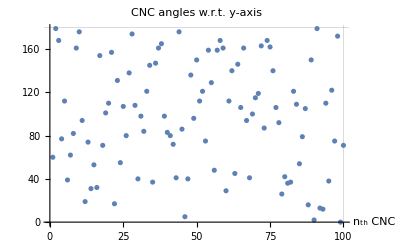
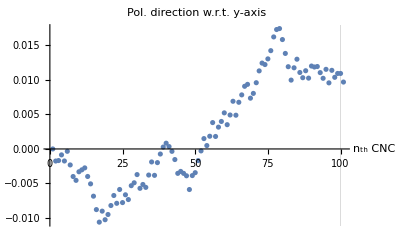
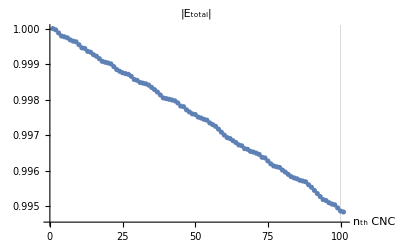
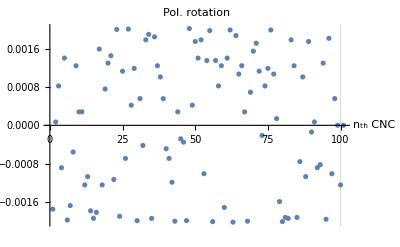

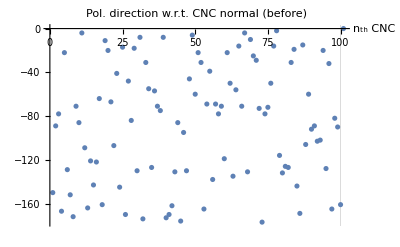
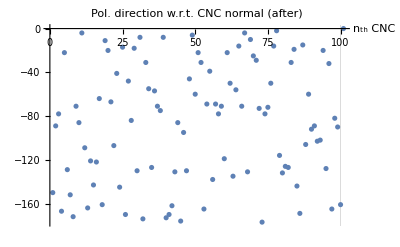

E_total after 100th CNC=0.994844+0. ⅈ

Final intensity after the 2nd polarizer=0.742141+0. ⅈ

```mathematica
{ListPlot[ϕra180,ImageSize->400,PlotRange->All,AxesLabel->{"n_th CNC",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},GridLines->{{100},{180}},AxesOrigin->{0,0},PlotLabel->"CNC angles w.r.t. y-axis"],
ListPlot[ψy,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. y-axis",GridLines->{{100},None}],
ListPlot[Etot,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"|E_total|",GridLines->{{100},None}],
ListPlot[(dψ),ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. rotation",GridLines->{{100},None}]}
{ListPlot[ϕbtn,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (before)",GridLines->{{100},None}],
ListPlot[ψres,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (after)",GridLines->{{100},None}]}

Print["E_total after 100th CNC=",Etot[[n+1]]]
Print["Final intensity after the 2nd polarizer=",PI]
```

#### Check numbers after each CNC

```mathematica
AppendTo[ϕra180,0];
AppendTo[ϕra180Norm,0];
ta1=Table[{i,ϕra180[[i]],ψy[[i]],ϕra180Norm[[i]],ϕbtn[[i]],ψres[[i]],dψ[[i]],"",ψy[[i]],dψ2[[i]]," ",Etot[[i]],ttot[[i]]},{i,1,n+1}];
PrependTo[ta1,{"nth CNC","CNC ang(180)","ψy","CNC norm ang","Ang btn(ϕbtn)","ψresult (CNC axis)","dψ(after-before)","+CNC norm","ψy","dψ2(ψ_(n + 1)-ψ_n)","-","E_tot","t_tot"}];
ta1//TableForm
```

nth CNC | CNC ang(180) | ψy | CNC norm ang | Ang btn(ϕbtn) | ψresult (CNC axis) | dψ(after-before) | +CNC norm | ψy | dψ2(ψ_(n + 1)-ψ_n) | - | E_tot | t_tot
1 | 60 | 1.×10^-9 | 150 | -150. | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 1.×10^-9 | -0.00174968+0. ⅈ |   | 1 | 0.999964+0. ⅈ
2 | 179 | -0.00174968+0. ⅈ | 89 | -89.0017+0. ⅈ | -89.0017+0. ⅈ | 0.0000703897+0. ⅈ |  | -0.00174968+0. ⅈ | 0.0000703897+0. ⅈ |   | 0.999964+0. ⅈ | 0.999912+0. ⅈ
3 | 168 | -0.00167929+0. ⅈ | 78 | -78.0017+0. ⅈ | -78.0009+0. ⅈ | 0.000821684+0. ⅈ |  | -0.00167929+0. ⅈ | 0.000821684+0. ⅈ |   | 0.999876+0. ⅈ | 0.999915+0. ⅈ
4 | 77 | -0.000857602+0. ⅈ | 167 | -167.001+0. ⅈ | -167.002+0. ⅈ | -0.000885598+0. ⅈ |  | -0.000857602+0. ⅈ | -0.000885598+0. ⅈ |   | 0.99979+0. ⅈ | 0.999978+0. ⅈ
5 | 112 | -0.0017432+0. ⅈ | 22 | -22.0017+0. ⅈ | -22.0003+0. ⅈ | 0.00140353+0. ⅈ |  | -0.0017432+0. ⅈ | 0.00140353+0. ⅈ |   | 0.999769+0. ⅈ | 0.999972+0. ⅈ
6 | 39 | -0.000339667+0. ⅈ | 129 | -129.+0. ⅈ | -129.002+0. ⅈ | -0.00197626+0. ⅈ |  | -0.000339667+0. ⅈ | -0.00197626+0. ⅈ |   | 0.999741+0. ⅈ | 0.999939+0. ⅈ
7 | 62 | -0.00231592+0. ⅈ | 152 | -152.002+0. ⅈ | -152.004+0. ⅈ | -0.00167485+0. ⅈ |  | -0.00231592+0. ⅈ | -0.00167485+0. ⅈ |   | 0.999681+0. ⅈ | 0.999966+0. ⅈ
8 | 82 | -0.00399078+0. ⅈ | 172 | -172.004+0. ⅈ | -172.005+0. ⅈ | -0.000556605+0. ⅈ |  | -0.00399078+0. ⅈ | -0.000556605+0. ⅈ |   | 0.999647+0. ⅈ | 0.999981+0. ⅈ
9 | 161 | -0.00454738+0. ⅈ | 71 | -71.0045+0. ⅈ | -71.0033+0. ⅈ | 0.00124366+0. ⅈ |  | -0.00454738+0. ⅈ | 0.00124366+0. ⅈ |   | 0.999628+0. ⅈ | 0.999919+0. ⅈ
10 | 176 | -0.00330373+0. ⅈ | 86 | -86.0033+0. ⅈ | -86.003+0. ⅈ | 0.000280963+0. ⅈ |  | -0.00330373+0. ⅈ | 0.000280963+0. ⅈ |   | 0.999547+0. ⅈ | 0.999912+0. ⅈ
11 | 94 | -0.00302276+0. ⅈ | 4 | -4.00302+0. ⅈ | -4.00274+0. ⅈ | 0.000281385+0. ⅈ |  | -0.00302276+0. ⅈ | 0.000281385+0. ⅈ |   | 0.999459+0. ⅈ | 0.999982+0. ⅈ
12 | 19 | -0.00274138+0. ⅈ | 109 | -109.003+0. ⅈ | -109.004+0. ⅈ | -0.00124406+0. ⅈ |  | -0.00274138+0. ⅈ | -0.00124406+0. ⅈ |   | 0.99944+0. ⅈ | 0.999919+0. ⅈ
13 | 74 | -0.00398544+0. ⅈ | 164 | -164.004+0. ⅈ | -164.005+0. ⅈ | -0.00107037+0. ⅈ |  | -0.00398544+0. ⅈ | -0.00107037+0. ⅈ |   | 0.999359+0. ⅈ | 0.999977+0. ⅈ
14 | 31 | -0.00505581+0. ⅈ | 121 | -121.005+0. ⅈ | -121.007+0. ⅈ | -0.00178409+0. ⅈ |  | -0.00505581+0. ⅈ | -0.00178409+0. ⅈ |   | 0.999336+0. ⅈ | 0.99993+0. ⅈ
15 | 53 | -0.00683991+0. ⅈ | 143 | -143.007+0. ⅈ | -143.009+0. ⅈ | -0.00194197+0. ⅈ |  | -0.00683991+0. ⅈ | -0.00194197+0. ⅈ |   | 0.999266+0. ⅈ | 0.999956+0. ⅈ
16 | 32 | -0.00878188+0. ⅈ | 122 | -122.009+0. ⅈ | -122.011+0. ⅈ | -0.00181621+0. ⅈ |  | -0.00878188+0. ⅈ | -0.00181621+0. ⅈ |   | 0.999223+0. ⅈ | 0.999931+0. ⅈ
17 | 154 | -0.0105981+0. ⅈ | 64 | -64.0106+0. ⅈ | -64.009+0. ⅈ | 0.00159166+0. ⅈ |  | -0.0105981+0. ⅈ | 0.00159166+0. ⅈ |   | 0.999154+0. ⅈ | 0.999925+0. ⅈ
18 | 71 | -0.00900643+0. ⅈ | 161 | -161.009+0. ⅈ | -161.01+0. ⅈ | -0.00124334+0. ⅈ |  | -0.00900643+0. ⅈ | -0.00124334+0. ⅈ |   | 0.999079+0. ⅈ | 0.999975+0. ⅈ
19 | 101 | -0.0102498+0. ⅈ | 11 | -11.0102+0. ⅈ | -11.0095+0. ⅈ | 0.000757496+0. ⅈ |  | -0.0102498+0. ⅈ | 0.000757496+0. ⅈ |   | 0.999054+0. ⅈ | 0.999979+0. ⅈ
20 | 110 | -0.00949227+0. ⅈ | 20 | -20.0095+0. ⅈ | -20.0082+0. ⅈ | 0.00129916+0. ⅈ |  | -0.00949227+0. ⅈ | 0.00129916+0. ⅈ |   | 0.999033+0. ⅈ | 0.999974+0. ⅈ
21 | 157 | -0.00819311+0. ⅈ | 67 | -67.0082+0. ⅈ | -67.0067+0. ⅈ | 0.00145298+0. ⅈ |  | -0.00819311+0. ⅈ | 0.00145298+0. ⅈ |   | 0.999007+0. ⅈ | 0.999922+0. ⅈ
22 | 17 | -0.00674013+0. ⅈ | 107 | -107.007+0. ⅈ | -107.008+0. ⅈ | -0.00113021+0. ⅈ |  | -0.00674013+0. ⅈ | -0.00113021+0. ⅈ |   | 0.99893+0. ⅈ | 0.999918+0. ⅈ
23 | 131 | -0.00787035+0. ⅈ | 41 | -41.0079+0. ⅈ | -41.0059+0. ⅈ | 0.00200079+0. ⅈ |  | -0.00787035+0. ⅈ | 0.00200079+0. ⅈ |   | 0.998847+0. ⅈ | 0.999952+0. ⅈ
24 | 55 | -0.00586955+0. ⅈ | 145 | -145.006+0. ⅈ | -145.008+0. ⅈ | -0.00189838+0. ⅈ |  | -0.00586955+0. ⅈ | -0.00189838+0. ⅈ |   | 0.998799+0. ⅈ | 0.999959+0. ⅈ
25 | 107 | -0.00776793+0. ⅈ | 17 | -17.0078+0. ⅈ | -17.0066+0. ⅈ | 0.00113021+0. ⅈ |  | -0.00776793+0. ⅈ | 0.00113021+0. ⅈ |   | 0.998758+0. ⅈ | 0.999976+0. ⅈ
26 | 80 | -0.00663772+0. ⅈ | 170 | -170.007+0. ⅈ | -170.007+0. ⅈ | -0.000690551+0. ⅈ |  | -0.00663772+0. ⅈ | -0.000690551+0. ⅈ |   | 0.998734+0. ⅈ | 0.99998+0. ⅈ
27 | 138 | -0.00732828+0. ⅈ | 48 | -48.0073+0. ⅈ | -48.0053+0. ⅈ | 0.00200927+0. ⅈ |  | -0.00732828+0. ⅈ | 0.00200927+0. ⅈ |   | 0.998714+0. ⅈ | 0.999943+0. ⅈ
28 | 174 | -0.005319+0. ⅈ | 84 | -84.0053+0. ⅈ | -84.0049+0. ⅈ | 0.00041971+0. ⅈ |  | -0.005319+0. ⅈ | 0.00041971+0. ⅈ |   | 0.998657+0. ⅈ | 0.999912+0. ⅈ
29 | 108 | -0.00489929+0. ⅈ | 18 | -18.0049+0. ⅈ | -18.0037+0. ⅈ | 0.0011878+0. ⅈ |  | -0.00489929+0. ⅈ | 0.0011878+0. ⅈ |   | 0.998569+0. ⅈ | 0.999975+0. ⅈ
30 | 40 | -0.00371149+0. ⅈ | 130 | -130.004+0. ⅈ | -130.006+0. ⅈ | -0.00198975+0. ⅈ |  | -0.00371149+0. ⅈ | -0.00198975+0. ⅈ |   | 0.998545+0. ⅈ | 0.999941+0. ⅈ
31 | 98 | -0.00570124+0. ⅈ | 8 | -8.0057+0. ⅈ | -8.00514+0. ⅈ | 0.000557262+0. ⅈ |  | -0.00570124+0. ⅈ | 0.000557262+0. ⅈ |   | 0.998485+0. ⅈ | 0.999981+0. ⅈ
32 | 84 | -0.00514398+0. ⅈ | 174 | -174.005+0. ⅈ | -174.006+0. ⅈ | -0.000419693+0. ⅈ |  | -0.00514398+0. ⅈ | -0.000419693+0. ⅈ |   | 0.998466+0. ⅈ | 0.999981+0. ⅈ
33 | 121 | -0.00556367+0. ⅈ | 31 | -31.0056+0. ⅈ | -31.0038+0. ⅈ | 0.00178405+0. ⅈ |  | -0.00556367+0. ⅈ | 0.00178405+0. ⅈ |   | 0.998447+0. ⅈ | 0.999963+0. ⅈ
34 | 145 | -0.00377962+0. ⅈ | 55 | -55.0038+0. ⅈ | -55.0019+0. ⅈ | 0.00189848+0. ⅈ |  | -0.00377962+0. ⅈ | 0.00189848+0. ⅈ |   | 0.998411+0. ⅈ | 0.999935+0. ⅈ
35 | 37 | -0.00188115+0. ⅈ | 127 | -127.002+0. ⅈ | -127.004+0. ⅈ | -0.00194218+0. ⅈ |  | -0.00188115+0. ⅈ | -0.00194218+0. ⅈ |   | 0.998345+0. ⅈ | 0.999937+0. ⅈ
36 | 147 | -0.00382332+0. ⅈ | 57 | -57.0038+0. ⅈ | -57.002+0. ⅈ | 0.00184563+0. ⅈ |  | -0.00382332+0. ⅈ | 0.00184563+0. ⅈ |   | 0.998283+0. ⅈ | 0.999932+0. ⅈ
37 | 161 | -0.00197769+0. ⅈ | 71 | -71.002+0. ⅈ | -71.0007+0. ⅈ | 0.0012438+0. ⅈ |  | -0.00197769+0. ⅈ | 0.0012438+0. ⅈ |   | 0.998215+0. ⅈ | 0.999919+0. ⅈ
38 | 165 | -0.000733891+0. ⅈ | 75 | -75.0007+0. ⅈ | -74.9997+0. ⅈ | 0.00101018+0. ⅈ |  | -0.000733891+0. ⅈ | 0.00101018+0. ⅈ |   | 0.998134+0. ⅈ | 0.999916+0. ⅈ
39 | 98 | 0.000276289+0. ⅈ | 8 | -7.99972+0. ⅈ | -7.99917+0. ⅈ | 0.000556857+0. ⅈ |  | 0.000276289+0. ⅈ | 0.000556857+0. ⅈ |   | 0.998051+0. ⅈ | 0.999981+0. ⅈ
40 | 83 | 0.000833146+0. ⅈ | 173 | -172.999+0. ⅈ | -173.+0. ⅈ | -0.000488816+0. ⅈ |  | 0.000833146+0. ⅈ | -0.000488816+0. ⅈ |   | 0.998031+0. ⅈ | 0.999981+0. ⅈ
41 | 80 | 0.00034433+0. ⅈ | 170 | -170.+0. ⅈ | -170.+0. ⅈ | -0.000691013+0. ⅈ |  | 0.00034433+0. ⅈ | -0.000691013+0. ⅈ |   | 0.998012+0. ⅈ | 0.99998+0. ⅈ
42 | 72 | -0.000346684+0. ⅈ | 162 | -162.+0. ⅈ | -162.002+0. ⅈ | -0.0011875+0. ⅈ |  | -0.000346684+0. ⅈ | -0.0011875+0. ⅈ |   | 0.997992+0. ⅈ | 0.999975+0. ⅈ
43 | 41 | -0.00153418+0. ⅈ | 131 | -131.002+0. ⅈ | -131.004+0. ⅈ | -0.00200075+0. ⅈ |  | -0.00153418+0. ⅈ | -0.00200075+0. ⅈ |   | 0.997968+0. ⅈ | 0.999942+0. ⅈ
44 | 176 | -0.00353494+0. ⅈ | 86 | -86.0035+0. ⅈ | -86.0033+0. ⅈ | 0.000280947+0. ⅈ |  | -0.00353494+0. ⅈ | 0.000280947+0. ⅈ |   | 0.99791+0. ⅈ | 0.999912+0. ⅈ
45 | 86 | -0.00325399+0. ⅈ | 176 | -176.003+0. ⅈ | -176.004+0. ⅈ | -0.000280947+0. ⅈ |  | -0.00325399+0. ⅈ | -0.000280947+0. ⅈ |   | 0.997822+0. ⅈ | 0.999982+0. ⅈ
46 | 5 | -0.00353494+0. ⅈ | 95 | -95.0035+0. ⅈ | -95.0039+0. ⅈ | -0.000351094+0. ⅈ |  | -0.00353494+0. ⅈ | -0.000351094+0. ⅈ |   | 0.997803+0. ⅈ | 0.999912+0. ⅈ
47 | 40 | -0.00388603+0. ⅈ | 130 | -130.004+0. ⅈ | -130.006+0. ⅈ | -0.00198975+0. ⅈ |  | -0.00388603+0. ⅈ | -0.00198975+0. ⅈ |   | 0.997716+0. ⅈ | 0.999941+0. ⅈ
48 | 136 | -0.00587578+0. ⅈ | 46 | -46.0059+0. ⅈ | -46.0039+0. ⅈ | 0.00201915+0. ⅈ |  | -0.00587578+0. ⅈ | 0.00201915+0. ⅈ |   | 0.997656+0. ⅈ | 0.999946+0. ⅈ
49 | 96 | -0.00385664+0. ⅈ | 6 | -6.00386+0. ⅈ | -6.00344+0. ⅈ | 0.000420314+0. ⅈ |  | -0.00385664+0. ⅈ | 0.000420314+0. ⅈ |   | 0.997602+0. ⅈ | 0.999981+0. ⅈ
50 | 150 | -0.00343632+0. ⅈ | 60 | -60.0034+0. ⅈ | -60.0017+0. ⅈ | 0.00174962+0. ⅈ |  | -0.00343632+0. ⅈ | 0.00174962+0. ⅈ |   | 0.997583+0. ⅈ | 0.999929+0. ⅈ
51 | 112 | -0.00168671+0. ⅈ | 22 | -22.0017+0. ⅈ | -22.0003+0. ⅈ | 0.00140353+0. ⅈ |  | -0.00168671+0. ⅈ | 0.00140353+0. ⅈ |   | 0.997513+0. ⅈ | 0.999972+0. ⅈ
52 | 121 | -0.000283177+0. ⅈ | 31 | -31.0003+0. ⅈ | -30.9985+0. ⅈ | 0.00178388+0. ⅈ |  | -0.000283177+0. ⅈ | 0.00178388+0. ⅈ |   | 0.997485+0. ⅈ | 0.999963+0. ⅈ
53 | 75 | 0.0015007+0. ⅈ | 165 | -164.998+0. ⅈ | -165.+0. ⅈ | -0.00101025+0. ⅈ |  | 0.0015007+0. ⅈ | -0.00101025+0. ⅈ |   | 0.997448+0. ⅈ | 0.999977+0. ⅈ
54 | 159 | 0.000490445+0. ⅈ | 69 | -68.9995+0. ⅈ | -68.9982+0. ⅈ | 0.00135196+0. ⅈ |  | 0.000490445+0. ⅈ | 0.00135196+0. ⅈ |   | 0.997426+0. ⅈ | 0.999921+0. ⅈ
55 | 129 | 0.00184241+0. ⅈ | 39 | -38.9982+0. ⅈ | -38.9962+0. ⅈ | 0.0019762+0. ⅈ |  | 0.00184241+0. ⅈ | 0.0019762+0. ⅈ |   | 0.997346+0. ⅈ | 0.999954+0. ⅈ
56 | 48 | 0.00381861+0. ⅈ | 138 | -137.996+0. ⅈ | -137.998+0. ⅈ | -0.00200934+0. ⅈ |  | 0.00381861+0. ⅈ | -0.00200934+0. ⅈ |   | 0.997301+0. ⅈ | 0.99995+0. ⅈ
57 | 159 | 0.00180926+0. ⅈ | 69 | -68.9982+0. ⅈ | -68.9968+0. ⅈ | 0.00135203+0. ⅈ |  | 0.00180926+0. ⅈ | 0.00135203+0. ⅈ |   | 0.997251+0. ⅈ | 0.999921+0. ⅈ
58 | 168 | 0.0031613+0. ⅈ | 78 | -77.9968+0. ⅈ | -77.996+0. ⅈ | 0.000821996+0. ⅈ |  | 0.0031613+0. ⅈ | 0.000821996+0. ⅈ |   | 0.997172+0. ⅈ | 0.999915+0. ⅈ
59 | 161 | 0.00398329+0. ⅈ | 71 | -70.996+0. ⅈ | -70.9948+0. ⅈ | 0.00124413+0. ⅈ |  | 0.00398329+0. ⅈ | 0.00124413+0. ⅈ |   | 0.997087+0. ⅈ | 0.999919+0. ⅈ
60 | 29 | 0.00522743+0. ⅈ | 119 | -118.995+0. ⅈ | -118.996+0. ⅈ | -0.00171322+0. ⅈ |  | 0.00522743+0. ⅈ | -0.00171322+0. ⅈ |   | 0.997006+0. ⅈ | 0.999928+0. ⅈ
61 | 112 | 0.0035142+0. ⅈ | 22 | -21.9965+0. ⅈ | -21.9951+0. ⅈ | 0.00140327+0. ⅈ |  | 0.0035142+0. ⅈ | 0.00140327+0. ⅈ |   | 0.996934+0. ⅈ | 0.999972+0. ⅈ
62 | 140 | 0.00491747+0. ⅈ | 50 | -49.9951+0. ⅈ | -49.9931+0. ⅈ | 0.00198977+0. ⅈ |  | 0.00491747+0. ⅈ | 0.00198977+0. ⅈ |   | 0.996907+0. ⅈ | 0.999941+0. ⅈ
63 | 45 | 0.00690723+0. ⅈ | 135 | -134.993+0. ⅈ | -134.995+0. ⅈ | -0.00202039+0. ⅈ |  | 0.00690723+0. ⅈ | -0.00202039+0. ⅈ |   | 0.996847+0. ⅈ | 0.999947+0. ⅈ
64 | 146 | 0.00488685+0. ⅈ | 56 | -55.9951+0. ⅈ | -55.9932+0. ⅈ | 0.00187343+0. ⅈ |  | 0.00488685+0. ⅈ | 0.00187343+0. ⅈ |   | 0.996794+0. ⅈ | 0.999934+0. ⅈ
65 | 106 | 0.00676027+0. ⅈ | 16 | -15.9932+0. ⅈ | -15.9922+0. ⅈ | 0.00107021+0. ⅈ |  | 0.00676027+0. ⅈ | 0.00107021+0. ⅈ |   | 0.996728+0. ⅈ | 0.999977+0. ⅈ
66 | 161 | 0.00783048+0. ⅈ | 71 | -70.9922+0. ⅈ | -70.9909+0. ⅈ | 0.00124434+0. ⅈ |  | 0.00783048+0. ⅈ | 0.00124434+0. ⅈ |   | 0.996705+0. ⅈ | 0.999919+0. ⅈ
67 | 94 | 0.00907482+0. ⅈ | 4 | -3.99093+0. ⅈ | -3.99064+0. ⅈ | 0.00028054+0. ⅈ |  | 0.00907482+0. ⅈ | 0.00028054+0. ⅈ |   | 0.996624+0. ⅈ | 0.999982+0. ⅈ
68 | 41 | 0.00935536+0. ⅈ | 131 | -130.991+0. ⅈ | -130.993+0. ⅈ | -0.00200064+0. ⅈ |  | 0.00935536+0. ⅈ | -0.00200064+0. ⅈ |   | 0.996606+0. ⅈ | 0.999942+0. ⅈ
69 | 100 | 0.00735472+0. ⅈ | 10 | -9.99265+0. ⅈ | -9.99195+0. ⅈ | 0.000690503+0. ⅈ |  | 0.00735472+0. ⅈ | 0.000690503+0. ⅈ |   | 0.996548+0. ⅈ | 0.99998+0. ⅈ
70 | 115 | 0.00804522+0. ⅈ | 25 | -24.992+0. ⅈ | -24.9904+0. ⅈ | 0.00154731+0. ⅈ |  | 0.00804522+0. ⅈ | 0.00154731+0. ⅈ |   | 0.996528+0. ⅈ | 0.999969+0. ⅈ
71 | 119 | 0.00959253+0. ⅈ | 29 | -28.9904+0. ⅈ | -28.9887+0. ⅈ | 0.001713+0. ⅈ |  | 0.00959253+0. ⅈ | 0.001713+0. ⅈ |   | 0.996497+0. ⅈ | 0.999965+0. ⅈ
72 | 163 | 0.0113055+0. ⅈ | 73 | -72.9887+0. ⅈ | -72.9876+0. ⅈ | 0.00113048+0. ⅈ |  | 0.0113055+0. ⅈ | 0.00113048+0. ⅈ |   | 0.996463+0. ⅈ | 0.999918+0. ⅈ
73 | 87 | 0.012436+0. ⅈ | 177 | -176.988+0. ⅈ | -176.988+0. ⅈ | -0.000212053+0. ⅈ |  | 0.012436+0. ⅈ | -0.000212053+0. ⅈ |   | 0.996381+0. ⅈ | 0.999982+0. ⅈ
74 | 168 | 0.012224+0. ⅈ | 78 | -77.9878+0. ⅈ | -77.987+0. ⅈ | 0.00082258+0. ⅈ |  | 0.012224+0. ⅈ | 0.00082258+0. ⅈ |   | 0.996363+0. ⅈ | 0.999915+0. ⅈ
75 | 162 | 0.0130465+0. ⅈ | 72 | -71.987+0. ⅈ | -71.9858+0. ⅈ | 0.00118833+0. ⅈ |  | 0.0130465+0. ⅈ | 0.00118833+0. ⅈ |   | 0.996278+0. ⅈ | 0.999918+0. ⅈ
76 | 140 | 0.0142349+0. ⅈ | 50 | -49.9858+0. ⅈ | -49.9838+0. ⅈ | 0.00198988+0. ⅈ |  | 0.0142349+0. ⅈ | 0.00198988+0. ⅈ |   | 0.996196+0. ⅈ | 0.999941+0. ⅈ
77 | 106 | 0.0162247+0. ⅈ | 16 | -15.9838+0. ⅈ | -15.9827+0. ⅈ | 0.00106964+0. ⅈ |  | 0.0162247+0. ⅈ | 0.00106964+0. ⅈ |   | 0.996137+0. ⅈ | 0.999977+0. ⅈ
78 | 92 | 0.0172944+0. ⅈ | 2 | -1.98271+0. ⅈ | -1.98257+0. ⅈ | 0.000139714+0. ⅈ |  | 0.0172944+0. ⅈ | 0.000139714+0. ⅈ |   | 0.996114+0. ⅈ | 0.999982+0. ⅈ
79 | 26 | 0.0174341+0. ⅈ | 116 | -115.983+0. ⅈ | -115.984+0. ⅈ | -0.00159137+0. ⅈ |  | 0.0174341+0. ⅈ | -0.00159137+0. ⅈ |   | 0.996096+0. ⅈ | 0.999925+0. ⅈ
80 | 42 | 0.0158427+0. ⅈ | 132 | -131.984+0. ⅈ | -131.986+0. ⅈ | -0.00200921+0. ⅈ |  | 0.0158427+0. ⅈ | -0.00200921+0. ⅈ |   | 0.996021+0. ⅈ | 0.999943+0. ⅈ
81 | 36 | 0.0138335+0. ⅈ | 126 | -125.986+0. ⅈ | -125.988+0. ⅈ | -0.00192122+0. ⅈ |  | 0.0138335+0. ⅈ | -0.00192122+0. ⅈ |   | 0.995965+0. ⅈ | 0.999936+0. ⅈ
82 | 37 | 0.0119123+0. ⅈ | 127 | -126.988+0. ⅈ | -126.99+0. ⅈ | -0.00194191+0. ⅈ |  | 0.0119123+0. ⅈ | -0.00194191+0. ⅈ |   | 0.995901+0. ⅈ | 0.999937+0. ⅈ
83 | 121 | 0.00997039+0. ⅈ | 31 | -30.99+0. ⅈ | -30.9882+0. ⅈ | 0.00178354+0. ⅈ |  | 0.00997039+0. ⅈ | 0.00178354+0. ⅈ |   | 0.995838+0. ⅈ | 0.999963+0. ⅈ
84 | 109 | 0.0117539+0. ⅈ | 19 | -18.9882+0. ⅈ | -18.987+0. ⅈ | 0.00124319+0. ⅈ |  | 0.0117539+0. ⅈ | 0.00124319+0. ⅈ |   | 0.995801+0. ⅈ | 0.999975+0. ⅈ
85 | 54 | 0.0129971+0. ⅈ | 144 | -143.987+0. ⅈ | -143.989+0. ⅈ | -0.00192177+0. ⅈ |  | 0.0129971+0. ⅈ | -0.00192177+0. ⅈ |   | 0.995776+0. ⅈ | 0.999958+0. ⅈ
86 | 79 | 0.0110754+0. ⅈ | 169 | -168.989+0. ⅈ | -168.99+0. ⅈ | -0.00075755+0. ⅈ |  | 0.0110754+0. ⅈ | -0.00075755+0. ⅈ |   | 0.995734+0. ⅈ | 0.999979+0. ⅈ
87 | 105 | 0.0103178+0. ⅈ | 15 | -14.9897+0. ⅈ | -14.9887+0. ⅈ | 0.00100953+0. ⅈ |  | 0.0103178+0. ⅈ | 0.00100953+0. ⅈ |   | 0.995713+0. ⅈ | 0.999977+0. ⅈ
88 | 16 | 0.0113273+0. ⅈ | 106 | -105.989+0. ⅈ | -105.99+0. ⅈ | -0.00107+0. ⅈ |  | 0.0113273+0. ⅈ | -0.00107+0. ⅈ |   | 0.995691+0. ⅈ | 0.999917+0. ⅈ
89 | 150 | 0.0102573+0. ⅈ | 60 | -59.9897+0. ⅈ | -59.988+0. ⅈ | 0.0017501+0. ⅈ |  | 0.0102573+0. ⅈ | 0.0017501+0. ⅈ |   | 0.995608+0. ⅈ | 0.999929+0. ⅈ
90 | 2 | 0.0120074+0. ⅈ | 92 | -91.988+0. ⅈ | -91.9881+0. ⅈ | -0.000140095+0. ⅈ |  | 0.0120074+0. ⅈ | -0.000140095+0. ⅈ |   | 0.995538+0. ⅈ | 0.999912+0. ⅈ
91 | 179 | 0.0118673+0. ⅈ | 89 | -88.9881+0. ⅈ | -88.9881+0. ⅈ | 0.0000713495+0. ⅈ |  | 0.0118673+0. ⅈ | 0.0000713495+0. ⅈ |   | 0.99545+0. ⅈ | 0.999912+0. ⅈ
92 | 13 | 0.0119387+0. ⅈ | 103 | -102.988+0. ⅈ | -102.989+0. ⅈ | -0.000884951+0. ⅈ |  | 0.0119387+0. ⅈ | -0.000884951+0. ⅈ |   | 0.995362+0. ⅈ | 0.999915+0. ⅈ
93 | 12 | 0.0110537+0. ⅈ | 102 | -101.989+0. ⅈ | -101.99+0. ⅈ | -0.00082108+0. ⅈ |  | 0.0110537+0. ⅈ | -0.00082108+0. ⅈ |   | 0.995277+0. ⅈ | 0.999915+0. ⅈ
94 | 110 | 0.0102327+0. ⅈ | 20 | -19.9898+0. ⅈ | -19.9885+0. ⅈ | 0.00129809+0. ⅈ |  | 0.0102327+0. ⅈ | 0.00129809+0. ⅈ |   | 0.995192+0. ⅈ | 0.999974+0. ⅈ
95 | 38 | 0.0115308+0. ⅈ | 128 | -127.988+0. ⅈ | -127.99+0. ⅈ | -0.00196019+0. ⅈ |  | 0.0115308+0. ⅈ | -0.00196019+0. ⅈ |   | 0.995166+0. ⅈ | 0.999938+0. ⅈ
96 | 122 | 0.00957056+0. ⅈ | 32 | -31.9904+0. ⅈ | -31.9886+0. ⅈ | 0.00181559+0. ⅈ |  | 0.00957056+0. ⅈ | 0.00181559+0. ⅈ |   | 0.995104+0. ⅈ | 0.999962+0. ⅈ
97 | 75 | 0.0113861+0. ⅈ | 165 | -164.989+0. ⅈ | -164.99+0. ⅈ | -0.00101086+0. ⅈ |  | 0.0113861+0. ⅈ | -0.00101086+0. ⅈ |   | 0.995067+0. ⅈ | 0.999977+0. ⅈ
98 | 172 | 0.0103753+0. ⅈ | 82 | -81.9896+0. ⅈ | -81.9891+0. ⅈ | 0.000557617+0. ⅈ |  | 0.0103753+0. ⅈ | 0.000557617+0. ⅈ |   | 0.995044+0. ⅈ | 0.999913+0. ⅈ
99 | 0 | 0.0109329+0. ⅈ | 90 | -89.9891+0. ⅈ | -89.9891+0. ⅈ | 7.71069×10^-7+0. ⅈ |  | 0.0109329+0. ⅈ | 7.71069×10^-7+0. ⅈ |   | 0.994957+0. ⅈ | 0.999912+0. ⅈ
100 | 71 | 0.0109337+0. ⅈ | 161 | -160.989+0. ⅈ | -160.99+0. ⅈ | -0.00124445+0. ⅈ |  | 0.0109337+0. ⅈ | -0.00124445+0. ⅈ |   | 0.994869+0. ⅈ | 0.999975+0. ⅈ
101 | 0 | 0.00968923+0. ⅈ | 0 | 0 | 0 | 0 |  | 0.00968923+0. ⅈ | 0 |   | 0.994844+0. ⅈ | 0

### 3) Helicoidal

#### Storage

```mathematica
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

Etot
ϕhe180

ψy
ϕbtn;
ψres;

dψ;
dψ2;
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150}

{1.×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Loop

```mathematica
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕhe180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕhe180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)
]
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕ1)*π/180])^2; (* I=(|Subscript[E, total]|*sinψ)^2 - Equation 5 *)
```

#### Check plots and final intensity

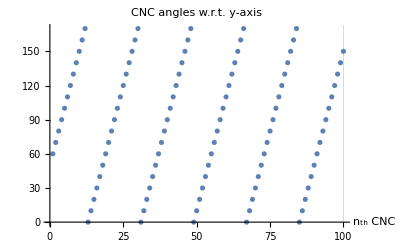
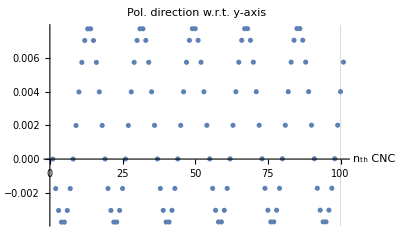
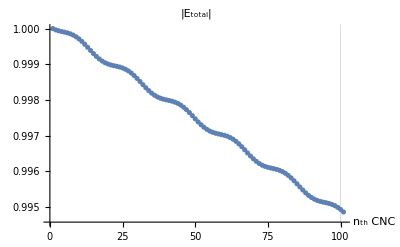
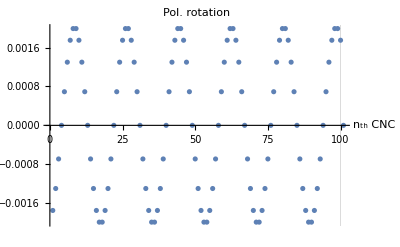

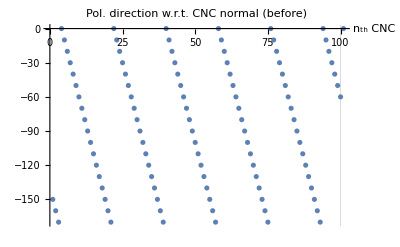
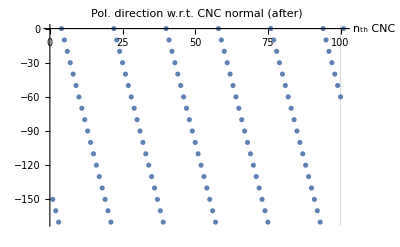

E_total after 100th CNC=0.994863+0. ⅈ

Final intensity after the 2nd polarizer=0.742228+0. ⅈ

```mathematica
{ListPlot[ϕhe180,ImageSize->400,PlotRange->All,AxesLabel->{"n_th CNC",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},GridLines->{{100},{180}},AxesOrigin->{0,0},PlotLabel->"CNC angles w.r.t. y-axis"],
ListPlot[ψy,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. y-axis",GridLines->{{100},None}],
ListPlot[Etot,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"|E_total|",GridLines->{{100},None}],
ListPlot[(dψ),ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. rotation",GridLines->{{100},None}]}
{ListPlot[ϕbtn,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (before)",GridLines->{{100},None}],
ListPlot[ψres,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (after)",GridLines->{{100},None}]}

Print["E_total after 100th CNC=",Etot[[n+1]]]
Print["Final intensity after the 2nd polarizer=",PI]
```

#### Check numbers after each CNC

```mathematica
AppendTo[ϕhe180,0];
AppendTo[ϕhe180Norm,0];
ta1=Table[{i,ϕhe180[[i]],ψy[[i]],ϕhe180Norm[[i]],ϕbtn[[i]],ψres[[i]],dψ[[i]],"",ψy[[i]],dψ2[[i]]," ",Etot[[i]],ttot[[i]]},{i,1,n+1}];
PrependTo[ta1,{"nth CNC","CNC ang(180)","ψy","CNC norm ang","Ang btn(ϕbtn)","ψresult (CNC axis)","dψ(after-before)","+CNC norm","ψy","dψ2(ψ_(n + 1)-ψ_n)","-","E_tot","t_tot"}];
ta1//TableForm
```

nth CNC | CNC ang(180) | ψy | CNC norm ang | Ang btn(ϕbtn) | ψresult (CNC axis) | dψ(after-before) | +CNC norm | ψy | dψ2(ψ_(n + 1)-ψ_n) | - | E_tot | t_tot
1 | 60 | 1.×10^-9 | 150 | -150. | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 1.×10^-9 | -0.00174968+0. ⅈ |   | 1 | 0.999964+0. ⅈ
2 | 70 | -0.00174968+0. ⅈ | 160 | -160.002+0. ⅈ | -160.003+0. ⅈ | -0.00129855+0. ⅈ |  | -0.00174968+0. ⅈ | -0.00129855+0. ⅈ |   | 0.999964+0. ⅈ | 0.999974+0. ⅈ
3 | 80 | -0.00304823+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.000690789+0. ⅈ |  | -0.00304823+0. ⅈ | -0.000690789+0. ⅈ |   | 0.999938+0. ⅈ | 0.99998+0. ⅈ
4 | 90 | -0.00373902+0. ⅈ | 0 | -0.00373902+0. ⅈ | -0.00373875+0. ⅈ | 2.63684×10^-7+0. ⅈ |  | -0.00373902+0. ⅈ | 2.63684×10^-7+0. ⅈ |   | 0.999918+0. ⅈ | 0.999982+0. ⅈ
5 | 100 | -0.00373875+0. ⅈ | 10 | -10.0037+0. ⅈ | -10.003+0. ⅈ | 0.000691238+0. ⅈ |  | -0.00373875+0. ⅈ | 0.000691238+0. ⅈ |   | 0.9999+0. ⅈ | 0.99998+0. ⅈ
6 | 110 | -0.00304751+0. ⅈ | 20 | -20.003+0. ⅈ | -20.0017+0. ⅈ | 0.00129881+0. ⅈ |  | -0.00304751+0. ⅈ | 0.00129881+0. ⅈ |   | 0.99988+0. ⅈ | 0.999974+0. ⅈ
7 | 120 | -0.0017487+0. ⅈ | 30 | -30.0017+0. ⅈ | -30.+0. ⅈ | 0.00174974+0. ⅈ |  | -0.0017487+0. ⅈ | 0.00174974+0. ⅈ |   | 0.999854+0. ⅈ | 0.999964+0. ⅈ
8 | 130 | 1.03528×10^-6+0. ⅈ | 40 | -40.+0. ⅈ | -39.998+0. ⅈ | 0.00198968+0. ⅈ |  | 1.03528×10^-6+0. ⅈ | 0.00198968+0. ⅈ |   | 0.999818+0. ⅈ | 0.999953+0. ⅈ
9 | 140 | 0.00199072+0. ⅈ | 50 | -49.998+0. ⅈ | -49.996+0. ⅈ | 0.00198973+0. ⅈ |  | 0.00199072+0. ⅈ | 0.00198973+0. ⅈ |   | 0.999771+0. ⅈ | 0.999941+0. ⅈ
10 | 150 | 0.00398045+0. ⅈ | 60 | -59.996+0. ⅈ | -59.9943+0. ⅈ | 0.00174988+0. ⅈ |  | 0.00398045+0. ⅈ | 0.00174988+0. ⅈ |   | 0.999712+0. ⅈ | 0.999929+0. ⅈ
11 | 160 | 0.00573033+0. ⅈ | 70 | -69.9943+0. ⅈ | -69.993+0. ⅈ | 0.00129903+0. ⅈ |  | 0.00573033+0. ⅈ | 0.00129903+0. ⅈ |   | 0.999641+0. ⅈ | 0.99992+0. ⅈ
12 | 170 | 0.00702935+0. ⅈ | 80 | -79.993+0. ⅈ | -79.9923+0. ⅈ | 0.000691502+0. ⅈ |  | 0.00702935+0. ⅈ | 0.000691502+0. ⅈ |   | 0.999561+0. ⅈ | 0.999914+0. ⅈ
13 | 0 | 0.00772085+0. ⅈ | 90 | -89.9923+0. ⅈ | -89.9923+0. ⅈ | 5.44531×10^-7+0. ⅈ |  | 0.00772085+0. ⅈ | 5.44531×10^-7+0. ⅈ |   | 0.999474+0. ⅈ | 0.999912+0. ⅈ
14 | 10 | 0.0077214+0. ⅈ | 100 | -99.9923+0. ⅈ | -99.993+0. ⅈ | -0.000690525+0. ⅈ |  | 0.0077214+0. ⅈ | -0.000690525+0. ⅈ |   | 0.999386+0. ⅈ | 0.999914+0. ⅈ
15 | 20 | 0.00703087+0. ⅈ | 110 | -109.993+0. ⅈ | -109.994+0. ⅈ | -0.00129834+0. ⅈ |  | 0.00703087+0. ⅈ | -0.00129834+0. ⅈ |   | 0.9993+0. ⅈ | 0.99992+0. ⅈ
16 | 30 | 0.00573254+0. ⅈ | 120 | -119.994+0. ⅈ | -119.996+0. ⅈ | -0.00174954+0. ⅈ |  | 0.00573254+0. ⅈ | -0.00174954+0. ⅈ |   | 0.999219+0. ⅈ | 0.999929+0. ⅈ
17 | 40 | 0.003983+0. ⅈ | 130 | -129.996+0. ⅈ | -129.998+0. ⅈ | -0.00198966+0. ⅈ |  | 0.003983+0. ⅈ | -0.00198966+0. ⅈ |   | 0.999149+0. ⅈ | 0.999941+0. ⅈ
18 | 50 | 0.00199334+0. ⅈ | 140 | -139.998+0. ⅈ | -140.+0. ⅈ | -0.00198971+0. ⅈ |  | 0.00199334+0. ⅈ | -0.00198971+0. ⅈ |   | 0.999089+0. ⅈ | 0.999953+0. ⅈ
19 | 60 | 3.63809×10^-6+0. ⅈ | 150 | -150.+0. ⅈ | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 3.63809×10^-6+0. ⅈ | -0.00174968+0. ⅈ |   | 0.999042+0. ⅈ | 0.999964+0. ⅈ
20 | 70 | -0.00174604+0. ⅈ | 160 | -160.002+0. ⅈ | -160.003+0. ⅈ | -0.00129855+0. ⅈ |  | -0.00174604+0. ⅈ | -0.00129855+0. ⅈ |   | 0.999007+0. ⅈ | 0.999974+0. ⅈ
21 | 80 | -0.00304459+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.000690789+0. ⅈ |  | -0.00304459+0. ⅈ | -0.000690789+0. ⅈ |   | 0.99898+0. ⅈ | 0.99998+0. ⅈ
22 | 90 | -0.00373538+0. ⅈ | 0 | -0.00373538+0. ⅈ | -0.00373512+0. ⅈ | 2.63428×10^-7+0. ⅈ |  | -0.00373538+0. ⅈ | 2.63428×10^-7+0. ⅈ |   | 0.99896+0. ⅈ | 0.999982+0. ⅈ
23 | 100 | -0.00373512+0. ⅈ | 10 | -10.0037+0. ⅈ | -10.003+0. ⅈ | 0.000691238+0. ⅈ |  | -0.00373512+0. ⅈ | 0.000691238+0. ⅈ |   | 0.998942+0. ⅈ | 0.99998+0. ⅈ
24 | 110 | -0.00304388+0. ⅈ | 20 | -20.003+0. ⅈ | -20.0017+0. ⅈ | 0.00129881+0. ⅈ |  | -0.00304388+0. ⅈ | 0.00129881+0. ⅈ |   | 0.998922+0. ⅈ | 0.999974+0. ⅈ
25 | 120 | -0.00174507+0. ⅈ | 30 | -30.0017+0. ⅈ | -30.+0. ⅈ | 0.00174974+0. ⅈ |  | -0.00174507+0. ⅈ | 0.00174974+0. ⅈ |   | 0.998896+0. ⅈ | 0.999964+0. ⅈ
26 | 130 | 4.67098×10^-6+0. ⅈ | 40 | -40.+0. ⅈ | -39.998+0. ⅈ | 0.00198968+0. ⅈ |  | 4.67098×10^-6+0. ⅈ | 0.00198968+0. ⅈ |   | 0.998861+0. ⅈ | 0.999953+0. ⅈ
27 | 140 | 0.00199435+0. ⅈ | 50 | -49.998+0. ⅈ | -49.996+0. ⅈ | 0.00198973+0. ⅈ |  | 0.00199435+0. ⅈ | 0.00198973+0. ⅈ |   | 0.998814+0. ⅈ | 0.999941+0. ⅈ
28 | 150 | 0.00398408+0. ⅈ | 60 | -59.996+0. ⅈ | -59.9943+0. ⅈ | 0.00174988+0. ⅈ |  | 0.00398408+0. ⅈ | 0.00174988+0. ⅈ |   | 0.998754+0. ⅈ | 0.999929+0. ⅈ
29 | 160 | 0.00573396+0. ⅈ | 70 | -69.9943+0. ⅈ | -69.993+0. ⅈ | 0.00129903+0. ⅈ |  | 0.00573396+0. ⅈ | 0.00129903+0. ⅈ |   | 0.998684+0. ⅈ | 0.99992+0. ⅈ
30 | 170 | 0.00703299+0. ⅈ | 80 | -79.993+0. ⅈ | -79.9923+0. ⅈ | 0.000691502+0. ⅈ |  | 0.00703299+0. ⅈ | 0.000691502+0. ⅈ |   | 0.998603+0. ⅈ | 0.999914+0. ⅈ
31 | 0 | 0.00772449+0. ⅈ | 90 | -89.9923+0. ⅈ | -89.9923+0. ⅈ | 5.44788×10^-7+0. ⅈ |  | 0.00772449+0. ⅈ | 5.44788×10^-7+0. ⅈ |   | 0.998517+0. ⅈ | 0.999912+0. ⅈ
32 | 10 | 0.00772504+0. ⅈ | 100 | -99.9923+0. ⅈ | -99.993+0. ⅈ | -0.000690524+0. ⅈ |  | 0.00772504+0. ⅈ | -0.000690524+0. ⅈ |   | 0.998429+0. ⅈ | 0.999914+0. ⅈ
33 | 20 | 0.00703451+0. ⅈ | 110 | -109.993+0. ⅈ | -109.994+0. ⅈ | -0.00129834+0. ⅈ |  | 0.00703451+0. ⅈ | -0.00129834+0. ⅈ |   | 0.998343+0. ⅈ | 0.99992+0. ⅈ
34 | 30 | 0.00573618+0. ⅈ | 120 | -119.994+0. ⅈ | -119.996+0. ⅈ | -0.00174954+0. ⅈ |  | 0.00573618+0. ⅈ | -0.00174954+0. ⅈ |   | 0.998262+0. ⅈ | 0.999929+0. ⅈ
35 | 40 | 0.00398664+0. ⅈ | 130 | -129.996+0. ⅈ | -129.998+0. ⅈ | -0.00198966+0. ⅈ |  | 0.00398664+0. ⅈ | -0.00198966+0. ⅈ |   | 0.998192+0. ⅈ | 0.999941+0. ⅈ
36 | 50 | 0.00199698+0. ⅈ | 140 | -139.998+0. ⅈ | -140.+0. ⅈ | -0.00198971+0. ⅈ |  | 0.00199698+0. ⅈ | -0.00198971+0. ⅈ |   | 0.998132+0. ⅈ | 0.999953+0. ⅈ
37 | 60 | 7.27517×10^-6+0. ⅈ | 150 | -150.+0. ⅈ | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 7.27517×10^-6+0. ⅈ | -0.00174968+0. ⅈ |   | 0.998085+0. ⅈ | 0.999964+0. ⅈ
38 | 70 | -0.0017424+0. ⅈ | 160 | -160.002+0. ⅈ | -160.003+0. ⅈ | -0.00129855+0. ⅈ |  | -0.0017424+0. ⅈ | -0.00129855+0. ⅈ |   | 0.99805+0. ⅈ | 0.999974+0. ⅈ
39 | 80 | -0.00304095+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.000690789+0. ⅈ |  | -0.00304095+0. ⅈ | -0.000690789+0. ⅈ |   | 0.998024+0. ⅈ | 0.99998+0. ⅈ
40 | 90 | -0.00373174+0. ⅈ | 0 | -0.00373174+0. ⅈ | -0.00373148+0. ⅈ | 2.63171×10^-7+0. ⅈ |  | -0.00373174+0. ⅈ | 2.63171×10^-7+0. ⅈ |   | 0.998004+0. ⅈ | 0.999982+0. ⅈ
41 | 100 | -0.00373148+0. ⅈ | 10 | -10.0037+0. ⅈ | -10.003+0. ⅈ | 0.000691238+0. ⅈ |  | -0.00373148+0. ⅈ | 0.000691238+0. ⅈ |   | 0.997986+0. ⅈ | 0.99998+0. ⅈ
42 | 110 | -0.00304024+0. ⅈ | 20 | -20.003+0. ⅈ | -20.0017+0. ⅈ | 0.00129881+0. ⅈ |  | -0.00304024+0. ⅈ | 0.00129881+0. ⅈ |   | 0.997966+0. ⅈ | 0.999974+0. ⅈ
43 | 120 | -0.00174143+0. ⅈ | 30 | -30.0017+0. ⅈ | -30.+0. ⅈ | 0.00174974+0. ⅈ |  | -0.00174143+0. ⅈ | 0.00174974+0. ⅈ |   | 0.99794+0. ⅈ | 0.999964+0. ⅈ
44 | 130 | 8.30668×10^-6+0. ⅈ | 40 | -40.+0. ⅈ | -39.998+0. ⅈ | 0.00198968+0. ⅈ |  | 8.30668×10^-6+0. ⅈ | 0.00198968+0. ⅈ |   | 0.997904+0. ⅈ | 0.999953+0. ⅈ
45 | 140 | 0.00199799+0. ⅈ | 50 | -49.998+0. ⅈ | -49.996+0. ⅈ | 0.00198973+0. ⅈ |  | 0.00199799+0. ⅈ | 0.00198973+0. ⅈ |   | 0.997857+0. ⅈ | 0.999941+0. ⅈ
46 | 150 | 0.00398772+0. ⅈ | 60 | -59.996+0. ⅈ | -59.9943+0. ⅈ | 0.00174988+0. ⅈ |  | 0.00398772+0. ⅈ | 0.00174988+0. ⅈ |   | 0.997798+0. ⅈ | 0.999929+0. ⅈ
47 | 160 | 0.0057376+0. ⅈ | 70 | -69.9943+0. ⅈ | -69.993+0. ⅈ | 0.00129903+0. ⅈ |  | 0.0057376+0. ⅈ | 0.00129903+0. ⅈ |   | 0.997727+0. ⅈ | 0.99992+0. ⅈ
48 | 170 | 0.00703662+0. ⅈ | 80 | -79.993+0. ⅈ | -79.9923+0. ⅈ | 0.000691503+0. ⅈ |  | 0.00703662+0. ⅈ | 0.000691503+0. ⅈ |   | 0.997647+0. ⅈ | 0.999914+0. ⅈ
49 | 0 | 0.00772813+0. ⅈ | 90 | -89.9923+0. ⅈ | -89.9923+0. ⅈ | 5.45044×10^-7+0. ⅈ |  | 0.00772813+0. ⅈ | 5.45044×10^-7+0. ⅈ |   | 0.997561+0. ⅈ | 0.999912+0. ⅈ
50 | 10 | 0.00772867+0. ⅈ | 100 | -99.9923+0. ⅈ | -99.993+0. ⅈ | -0.000690524+0. ⅈ |  | 0.00772867+0. ⅈ | -0.000690524+0. ⅈ |   | 0.997473+0. ⅈ | 0.999914+0. ⅈ
51 | 20 | 0.00703815+0. ⅈ | 110 | -109.993+0. ⅈ | -109.994+0. ⅈ | -0.00129834+0. ⅈ |  | 0.00703815+0. ⅈ | -0.00129834+0. ⅈ |   | 0.997386+0. ⅈ | 0.99992+0. ⅈ
52 | 30 | 0.00573981+0. ⅈ | 120 | -119.994+0. ⅈ | -119.996+0. ⅈ | -0.00174954+0. ⅈ |  | 0.00573981+0. ⅈ | -0.00174954+0. ⅈ |   | 0.997306+0. ⅈ | 0.999929+0. ⅈ
53 | 40 | 0.00399028+0. ⅈ | 130 | -129.996+0. ⅈ | -129.998+0. ⅈ | -0.00198966+0. ⅈ |  | 0.00399028+0. ⅈ | -0.00198966+0. ⅈ |   | 0.997236+0. ⅈ | 0.999941+0. ⅈ
54 | 50 | 0.00200062+0. ⅈ | 140 | -139.998+0. ⅈ | -140.+0. ⅈ | -0.00198971+0. ⅈ |  | 0.00200062+0. ⅈ | -0.00198971+0. ⅈ |   | 0.997177+0. ⅈ | 0.999953+0. ⅈ
55 | 60 | 0.0000109123+0. ⅈ | 150 | -150.+0. ⅈ | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 0.0000109123+0. ⅈ | -0.00174968+0. ⅈ |   | 0.99713+0. ⅈ | 0.999964+0. ⅈ
56 | 70 | -0.00173876+0. ⅈ | 160 | -160.002+0. ⅈ | -160.003+0. ⅈ | -0.00129855+0. ⅈ |  | -0.00173876+0. ⅈ | -0.00129855+0. ⅈ |   | 0.997094+0. ⅈ | 0.999974+0. ⅈ
57 | 80 | -0.00303732+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.000690789+0. ⅈ |  | -0.00303732+0. ⅈ | -0.000690789+0. ⅈ |   | 0.997068+0. ⅈ | 0.99998+0. ⅈ
58 | 90 | -0.00372811+0. ⅈ | 0 | -0.00372811+0. ⅈ | -0.00372784+0. ⅈ | 2.62915×10^-7+0. ⅈ |  | -0.00372811+0. ⅈ | 2.62915×10^-7+0. ⅈ |   | 0.997048+0. ⅈ | 0.999982+0. ⅈ
59 | 100 | -0.00372784+0. ⅈ | 10 | -10.0037+0. ⅈ | -10.003+0. ⅈ | 0.000691238+0. ⅈ |  | -0.00372784+0. ⅈ | 0.000691238+0. ⅈ |   | 0.99703+0. ⅈ | 0.99998+0. ⅈ
60 | 110 | -0.00303661+0. ⅈ | 20 | -20.003+0. ⅈ | -20.0017+0. ⅈ | 0.00129881+0. ⅈ |  | -0.00303661+0. ⅈ | 0.00129881+0. ⅈ |   | 0.99701+0. ⅈ | 0.999974+0. ⅈ
61 | 120 | -0.0017378+0. ⅈ | 30 | -30.0017+0. ⅈ | -30.+0. ⅈ | 0.00174974+0. ⅈ |  | -0.0017378+0. ⅈ | 0.00174974+0. ⅈ |   | 0.996984+0. ⅈ | 0.999964+0. ⅈ
62 | 130 | 0.0000119424+0. ⅈ | 40 | -40.+0. ⅈ | -39.998+0. ⅈ | 0.00198968+0. ⅈ |  | 0.0000119424+0. ⅈ | 0.00198968+0. ⅈ |   | 0.996948+0. ⅈ | 0.999953+0. ⅈ
63 | 140 | 0.00200162+0. ⅈ | 50 | -49.998+0. ⅈ | -49.996+0. ⅈ | 0.00198973+0. ⅈ |  | 0.00200162+0. ⅈ | 0.00198973+0. ⅈ |   | 0.996901+0. ⅈ | 0.999941+0. ⅈ
64 | 150 | 0.00399135+0. ⅈ | 60 | -59.996+0. ⅈ | -59.9943+0. ⅈ | 0.00174988+0. ⅈ |  | 0.00399135+0. ⅈ | 0.00174988+0. ⅈ |   | 0.996842+0. ⅈ | 0.999929+0. ⅈ
65 | 160 | 0.00574123+0. ⅈ | 70 | -69.9943+0. ⅈ | -69.993+0. ⅈ | 0.00129903+0. ⅈ |  | 0.00574123+0. ⅈ | 0.00129903+0. ⅈ |   | 0.996771+0. ⅈ | 0.99992+0. ⅈ
66 | 170 | 0.00704026+0. ⅈ | 80 | -79.993+0. ⅈ | -79.9923+0. ⅈ | 0.000691503+0. ⅈ |  | 0.00704026+0. ⅈ | 0.000691503+0. ⅈ |   | 0.996692+0. ⅈ | 0.999914+0. ⅈ
67 | 0 | 0.00773176+0. ⅈ | 90 | -89.9923+0. ⅈ | -89.9923+0. ⅈ | 5.45301×10^-7+0. ⅈ |  | 0.00773176+0. ⅈ | 5.45301×10^-7+0. ⅈ |   | 0.996605+0. ⅈ | 0.999912+0. ⅈ
68 | 10 | 0.00773231+0. ⅈ | 100 | -99.9923+0. ⅈ | -99.993+0. ⅈ | -0.000690524+0. ⅈ |  | 0.00773231+0. ⅈ | -0.000690524+0. ⅈ |   | 0.996517+0. ⅈ | 0.999914+0. ⅈ
69 | 20 | 0.00704178+0. ⅈ | 110 | -109.993+0. ⅈ | -109.994+0. ⅈ | -0.00129834+0. ⅈ |  | 0.00704178+0. ⅈ | -0.00129834+0. ⅈ |   | 0.996431+0. ⅈ | 0.99992+0. ⅈ
70 | 30 | 0.00574345+0. ⅈ | 120 | -119.994+0. ⅈ | -119.996+0. ⅈ | -0.00174954+0. ⅈ |  | 0.00574345+0. ⅈ | -0.00174954+0. ⅈ |   | 0.996351+0. ⅈ | 0.999929+0. ⅈ
71 | 40 | 0.00399391+0. ⅈ | 130 | -129.996+0. ⅈ | -129.998+0. ⅈ | -0.00198966+0. ⅈ |  | 0.00399391+0. ⅈ | -0.00198966+0. ⅈ |   | 0.996281+0. ⅈ | 0.999941+0. ⅈ
72 | 50 | 0.00200426+0. ⅈ | 140 | -139.998+0. ⅈ | -140.+0. ⅈ | -0.00198971+0. ⅈ |  | 0.00200426+0. ⅈ | -0.00198971+0. ⅈ |   | 0.996221+0. ⅈ | 0.999953+0. ⅈ
73 | 60 | 0.0000145493+0. ⅈ | 150 | -150.+0. ⅈ | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 0.0000145493+0. ⅈ | -0.00174968+0. ⅈ |   | 0.996175+0. ⅈ | 0.999964+0. ⅈ
74 | 70 | -0.00173513+0. ⅈ | 160 | -160.002+0. ⅈ | -160.003+0. ⅈ | -0.00129855+0. ⅈ |  | -0.00173513+0. ⅈ | -0.00129855+0. ⅈ |   | 0.996139+0. ⅈ | 0.999974+0. ⅈ
75 | 80 | -0.00303368+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.00069079+0. ⅈ |  | -0.00303368+0. ⅈ | -0.00069079+0. ⅈ |   | 0.996113+0. ⅈ | 0.99998+0. ⅈ
76 | 90 | -0.00372447+0. ⅈ | 0 | -0.00372447+0. ⅈ | -0.00372421+0. ⅈ | 2.62658×10^-7+0. ⅈ |  | -0.00372447+0. ⅈ | 2.62658×10^-7+0. ⅈ |   | 0.996093+0. ⅈ | 0.999982+0. ⅈ
77 | 100 | -0.00372421+0. ⅈ | 10 | -10.0037+0. ⅈ | -10.003+0. ⅈ | 0.000691237+0. ⅈ |  | -0.00372421+0. ⅈ | 0.000691237+0. ⅈ |   | 0.996075+0. ⅈ | 0.99998+0. ⅈ
78 | 110 | -0.00303297+0. ⅈ | 20 | -20.003+0. ⅈ | -20.0017+0. ⅈ | 0.00129881+0. ⅈ |  | -0.00303297+0. ⅈ | 0.00129881+0. ⅈ |   | 0.996055+0. ⅈ | 0.999974+0. ⅈ
79 | 120 | -0.00173416+0. ⅈ | 30 | -30.0017+0. ⅈ | -30.+0. ⅈ | 0.00174974+0. ⅈ |  | -0.00173416+0. ⅈ | 0.00174974+0. ⅈ |   | 0.996029+0. ⅈ | 0.999964+0. ⅈ
80 | 130 | 0.0000155781+0. ⅈ | 40 | -40.+0. ⅈ | -39.998+0. ⅈ | 0.00198968+0. ⅈ |  | 0.0000155781+0. ⅈ | 0.00198968+0. ⅈ |   | 0.995993+0. ⅈ | 0.999953+0. ⅈ
81 | 140 | 0.00200526+0. ⅈ | 50 | -49.998+0. ⅈ | -49.996+0. ⅈ | 0.00198973+0. ⅈ |  | 0.00200526+0. ⅈ | 0.00198973+0. ⅈ |   | 0.995947+0. ⅈ | 0.999941+0. ⅈ
82 | 150 | 0.00399499+0. ⅈ | 60 | -59.996+0. ⅈ | -59.9943+0. ⅈ | 0.00174988+0. ⅈ |  | 0.00399499+0. ⅈ | 0.00174988+0. ⅈ |   | 0.995887+0. ⅈ | 0.999929+0. ⅈ
83 | 160 | 0.00574487+0. ⅈ | 70 | -69.9943+0. ⅈ | -69.993+0. ⅈ | 0.00129903+0. ⅈ |  | 0.00574487+0. ⅈ | 0.00129903+0. ⅈ |   | 0.995817+0. ⅈ | 0.99992+0. ⅈ
84 | 170 | 0.0070439+0. ⅈ | 80 | -79.993+0. ⅈ | -79.9923+0. ⅈ | 0.000691503+0. ⅈ |  | 0.0070439+0. ⅈ | 0.000691503+0. ⅈ |   | 0.995737+0. ⅈ | 0.999914+0. ⅈ
85 | 0 | 0.0077354+0. ⅈ | 90 | -89.9923+0. ⅈ | -89.9923+0. ⅈ | 5.45557×10^-7+0. ⅈ |  | 0.0077354+0. ⅈ | 5.45557×10^-7+0. ⅈ |   | 0.995651+0. ⅈ | 0.999912+0. ⅈ
86 | 10 | 0.00773594+0. ⅈ | 100 | -99.9923+0. ⅈ | -99.993+0. ⅈ | -0.000690524+0. ⅈ |  | 0.00773594+0. ⅈ | -0.000690524+0. ⅈ |   | 0.995563+0. ⅈ | 0.999914+0. ⅈ
87 | 20 | 0.00704542+0. ⅈ | 110 | -109.993+0. ⅈ | -109.994+0. ⅈ | -0.00129833+0. ⅈ |  | 0.00704542+0. ⅈ | -0.00129833+0. ⅈ |   | 0.995477+0. ⅈ | 0.99992+0. ⅈ
88 | 30 | 0.00574709+0. ⅈ | 120 | -119.994+0. ⅈ | -119.996+0. ⅈ | -0.00174954+0. ⅈ |  | 0.00574709+0. ⅈ | -0.00174954+0. ⅈ |   | 0.995397+0. ⅈ | 0.999929+0. ⅈ
89 | 40 | 0.00399755+0. ⅈ | 130 | -129.996+0. ⅈ | -129.998+0. ⅈ | -0.00198966+0. ⅈ |  | 0.00399755+0. ⅈ | -0.00198966+0. ⅈ |   | 0.995326+0. ⅈ | 0.999941+0. ⅈ
90 | 50 | 0.00200789+0. ⅈ | 140 | -139.998+0. ⅈ | -140.+0. ⅈ | -0.00198971+0. ⅈ |  | 0.00200789+0. ⅈ | -0.00198971+0. ⅈ |   | 0.995267+0. ⅈ | 0.999953+0. ⅈ
91 | 60 | 0.0000181864+0. ⅈ | 150 | -150.+0. ⅈ | -150.002+0. ⅈ | -0.00174968+0. ⅈ |  | 0.0000181864+0. ⅈ | -0.00174968+0. ⅈ |   | 0.99522+0. ⅈ | 0.999964+0. ⅈ
92 | 70 | -0.00173149+0. ⅈ | 160 | -160.002+0. ⅈ | -160.003+0. ⅈ | -0.00129855+0. ⅈ |  | -0.00173149+0. ⅈ | -0.00129855+0. ⅈ |   | 0.995185+0. ⅈ | 0.999974+0. ⅈ
93 | 80 | -0.00303004+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.00069079+0. ⅈ |  | -0.00303004+0. ⅈ | -0.00069079+0. ⅈ |   | 0.995159+0. ⅈ | 0.99998+0. ⅈ
94 | 90 | -0.00372083+0. ⅈ | 0 | -0.00372083+0. ⅈ | -0.00372057+0. ⅈ | 2.62402×10^-7+0. ⅈ |  | -0.00372083+0. ⅈ | 2.62402×10^-7+0. ⅈ |   | 0.995139+0. ⅈ | 0.999982+0. ⅈ
95 | 100 | -0.00372057+0. ⅈ | 10 | -10.0037+0. ⅈ | -10.003+0. ⅈ | 0.000691237+0. ⅈ |  | -0.00372057+0. ⅈ | 0.000691237+0. ⅈ |   | 0.995121+0. ⅈ | 0.99998+0. ⅈ
96 | 110 | -0.00302933+0. ⅈ | 20 | -20.003+0. ⅈ | -20.0017+0. ⅈ | 0.00129881+0. ⅈ |  | -0.00302933+0. ⅈ | 0.00129881+0. ⅈ |   | 0.995101+0. ⅈ | 0.999974+0. ⅈ
97 | 120 | -0.00173052+0. ⅈ | 30 | -30.0017+0. ⅈ | -30.+0. ⅈ | 0.00174974+0. ⅈ |  | -0.00173052+0. ⅈ | 0.00174974+0. ⅈ |   | 0.995075+0. ⅈ | 0.999964+0. ⅈ
98 | 130 | 0.0000192138+0. ⅈ | 40 | -40.+0. ⅈ | -39.998+0. ⅈ | 0.00198968+0. ⅈ |  | 0.0000192138+0. ⅈ | 0.00198968+0. ⅈ |   | 0.99504+0. ⅈ | 0.999953+0. ⅈ
99 | 140 | 0.0020089+0. ⅈ | 50 | -49.998+0. ⅈ | -49.996+0. ⅈ | 0.00198973+0. ⅈ |  | 0.0020089+0. ⅈ | 0.00198973+0. ⅈ |   | 0.994993+0. ⅈ | 0.999941+0. ⅈ
100 | 150 | 0.00399863+0. ⅈ | 60 | -59.996+0. ⅈ | -59.9943+0. ⅈ | 0.00174988+0. ⅈ |  | 0.00399863+0. ⅈ | 0.00174988+0. ⅈ |   | 0.994934+0. ⅈ | 0.999929+0. ⅈ
101 | 0 | 0.00574851+0. ⅈ | 0 | 0 | 0 | 0 |  | 0.00574851+0. ⅈ | 0 |   | 0.994863+0. ⅈ | 0

### 4) Uniaxial

#### Storage

```mathematica
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

Etot
ϕun180

ψy
ϕbtn;
ψres;

dψ;
dψ2;
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{100,101,84,91,62,86,87,61,92,80,99,92,90,94,81,80,84,72,80,99,82,108,101,88,111,78,85,81,109,101,111,85,94,105,78,82,98,86,87,101,78,99,93,91,79,87,91,97,118,88,84,87,86,90,94,96,81,100,72,97,89,96,86,93,98,84,95,97,95,95,96,91,93,106,75,87,80,94,77,97,108,93,121,108,92,76,81,80,71,100,93,115,108,82,94,77,79,87,80,98}

{1.×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Loop

```mathematica
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕun180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕun180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)

]

PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕ1)*π/180])^2; (* I=(|Subscript[E, total]|*sinψ)^2 - Equation 5 *)
```

#### Check plots and final intensity

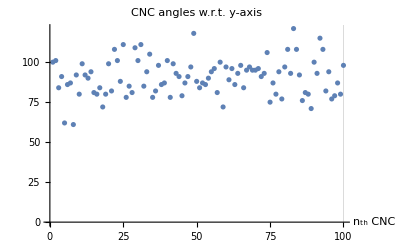
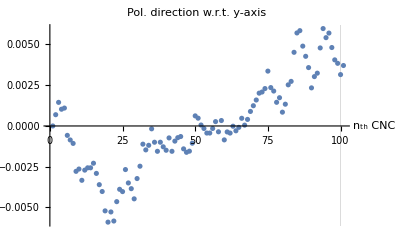
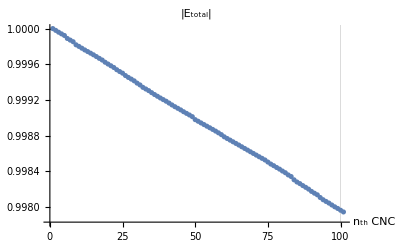
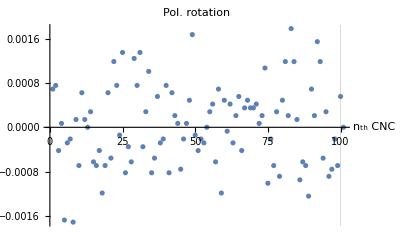

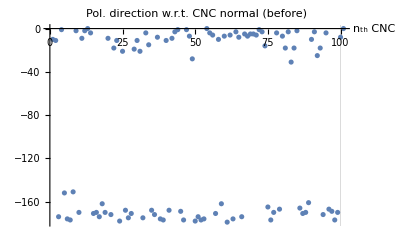
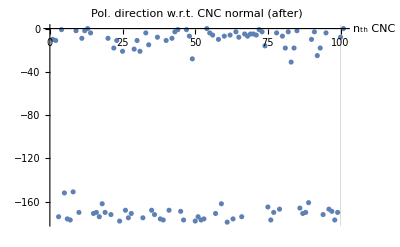

E_total after 100th CNC=0.997945+0. ⅈ

Final intensity after the 2nd polarizer=0.746864+0. ⅈ

```mathematica
{ListPlot[ϕun180,ImageSize->400,PlotRange->All,AxesLabel->{"n_th CNC",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},GridLines->{{100},{180}},AxesOrigin->{0,0},PlotLabel->"CNC angles w.r.t. y-axis"],
ListPlot[ψy,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. y-axis",GridLines->{{100},None}],
ListPlot[Etot,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"|E_total|",GridLines->{{100},None}],
ListPlot[(dψ),ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. rotation",GridLines->{{100},None}]}
{ListPlot[ϕbtn,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (before)",GridLines->{{100},None}],
ListPlot[ψres,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (after)",GridLines->{{100},None}]}

Print["E_total after 100th CNC=",Etot[[n+1]]]
Print["Final intensity after the 2nd polarizer=",PI]
```

#### Check numbers after each CNC

```mathematica
AppendTo[ϕun180,0];
AppendTo[ϕun180Norm,0];
ta1=Table[{i,ϕun180[[i]],ψy[[i]],ϕun180Norm[[i]],ϕbtn[[i]],ψres[[i]],dψ[[i]],"",ψy[[i]],dψ2[[i]]," ",Etot[[i]],ttot[[i]]},{i,1,n+1}];
PrependTo[ta1,{"nth CNC","CNC ang(180)","ψy","CNC norm ang","Ang btn(ϕbtn)","ψresult (CNC axis)","dψ(after-before)","+CNC norm","ψy","dψ2(ψ_(n + 1)-ψ_n)","-","E_tot","t_tot"}];
ta1//TableForm
```

nth CNC | CNC ang(180) | ψy | CNC norm ang | Ang btn(ϕbtn) | ψresult (CNC axis) | dψ(after-before) | +CNC norm | ψy | dψ2(ψ_(n + 1)-ψ_n) | - | E_tot | t_tot
1 | 100 | 1.×10^-9 | 10 | -10. | -9.99931+0. ⅈ | 0.000690991+0. ⅈ |  | 1.×10^-9 | 0.000690991+0. ⅈ |   | 1 | 0.99998+0. ⅈ
2 | 101 | 0.000690992+0. ⅈ | 11 | -10.9993+0. ⅈ | -10.9986+0. ⅈ | 0.000756781+0. ⅈ |  | 0.000690992+0. ⅈ | 0.000756781+0. ⅈ |   | 0.99998+0. ⅈ | 0.999979+0. ⅈ
3 | 84 | 0.00144777+0. ⅈ | 174 | -173.999+0. ⅈ | -173.999+0. ⅈ | -0.000420148+0. ⅈ |  | 0.00144777+0. ⅈ | -0.000420148+0. ⅈ |   | 0.999959+0. ⅈ | 0.999981+0. ⅈ
4 | 91 | 0.00102762+0. ⅈ | 1 | -0.998972+0. ⅈ | -0.998902+0. ⅈ | 0.0000704356+0. ⅈ |  | 0.00102762+0. ⅈ | 0.0000704356+0. ⅈ |   | 0.999941+0. ⅈ | 0.999982+0. ⅈ
5 | 62 | 0.00109806+0. ⅈ | 152 | -151.999+0. ⅈ | -152.001+0. ⅈ | -0.00167499+0. ⅈ |  | 0.00109806+0. ⅈ | -0.00167499+0. ⅈ |   | 0.999923+0. ⅈ | 0.999966+0. ⅈ
6 | 86 | -0.000576928+0. ⅈ | 176 | -176.001+0. ⅈ | -176.001+0. ⅈ | -0.000281134+0. ⅈ |  | -0.000576928+0. ⅈ | -0.000281134+0. ⅈ |   | 0.999889+0. ⅈ | 0.999982+0. ⅈ
7 | 87 | -0.000858061+0. ⅈ | 177 | -177.001+0. ⅈ | -177.001+0. ⅈ | -0.00021112+0. ⅈ |  | -0.000858061+0. ⅈ | -0.00021112+0. ⅈ |   | 0.999871+0. ⅈ | 0.999982+0. ⅈ
8 | 61 | -0.00106918+0. ⅈ | 151 | -151.001+0. ⅈ | -151.003+0. ⅈ | -0.00171331+0. ⅈ |  | -0.00106918+0. ⅈ | -0.00171331+0. ⅈ |   | 0.999853+0. ⅈ | 0.999965+0. ⅈ
9 | 92 | -0.0027825+0. ⅈ | 2 | -2.00278+0. ⅈ | -2.00264+0. ⅈ | 0.000141126+0. ⅈ |  | -0.0027825+0. ⅈ | 0.000141126+0. ⅈ |   | 0.999818+0. ⅈ | 0.999982+0. ⅈ
10 | 80 | -0.00264137+0. ⅈ | 170 | -170.003+0. ⅈ | -170.003+0. ⅈ | -0.000690816+0. ⅈ |  | -0.00264137+0. ⅈ | -0.000690816+0. ⅈ |   | 0.9998+0. ⅈ | 0.99998+0. ⅈ
11 | 99 | -0.00333219+0. ⅈ | 9 | -9.00333+0. ⅈ | -9.00271+0. ⅈ | 0.000624537+0. ⅈ |  | -0.00333219+0. ⅈ | 0.000624537+0. ⅈ |   | 0.99978+0. ⅈ | 0.99998+0. ⅈ
12 | 92 | -0.00270765+0. ⅈ | 2 | -2.00271+0. ⅈ | -2.00257+0. ⅈ | 0.000141121+0. ⅈ |  | -0.00270765+0. ⅈ | 0.000141121+0. ⅈ |   | 0.99976+0. ⅈ | 0.999982+0. ⅈ
13 | 90 | -0.00256653+0. ⅈ | 0 | -0.00256653+0. ⅈ | -0.00256635+0. ⅈ | 1.80998×10^-7+0. ⅈ |  | -0.00256653+0. ⅈ | 1.80998×10^-7+0. ⅈ |   | 0.999742+0. ⅈ | 0.999982+0. ⅈ
14 | 94 | -0.00256635+0. ⅈ | 4 | -4.00257+0. ⅈ | -4.00228+0. ⅈ | 0.000281353+0. ⅈ |  | -0.00256635+0. ⅈ | 0.000281353+0. ⅈ |   | 0.999724+0. ⅈ | 0.999982+0. ⅈ
15 | 81 | -0.00228499+0. ⅈ | 171 | -171.002+0. ⅈ | -171.003+0. ⅈ | -0.00062416+0. ⅈ |  | -0.00228499+0. ⅈ | -0.00062416+0. ⅈ |   | 0.999706+0. ⅈ | 0.99998+0. ⅈ
16 | 80 | -0.00290915+0. ⅈ | 170 | -170.003+0. ⅈ | -170.004+0. ⅈ | -0.000690798+0. ⅈ |  | -0.00290915+0. ⅈ | -0.000690798+0. ⅈ |   | 0.999686+0. ⅈ | 0.99998+0. ⅈ
17 | 84 | -0.00359995+0. ⅈ | 174 | -174.004+0. ⅈ | -174.004+0. ⅈ | -0.0004198+0. ⅈ |  | -0.00359995+0. ⅈ | -0.0004198+0. ⅈ |   | 0.999666+0. ⅈ | 0.999981+0. ⅈ
18 | 72 | -0.00401975+0. ⅈ | 162 | -162.004+0. ⅈ | -162.005+0. ⅈ | -0.00118729+0. ⅈ |  | -0.00401975+0. ⅈ | -0.00118729+0. ⅈ |   | 0.999647+0. ⅈ | 0.999975+0. ⅈ
19 | 80 | -0.00520704+0. ⅈ | 170 | -170.005+0. ⅈ | -170.006+0. ⅈ | -0.000690646+0. ⅈ |  | -0.00520704+0. ⅈ | -0.000690646+0. ⅈ |   | 0.999623+0. ⅈ | 0.99998+0. ⅈ
20 | 99 | -0.00589769+0. ⅈ | 9 | -9.0059+0. ⅈ | -9.00527+0. ⅈ | 0.000624709+0. ⅈ |  | -0.00589769+0. ⅈ | 0.000624709+0. ⅈ |   | 0.999603+0. ⅈ | 0.99998+0. ⅈ
21 | 82 | -0.00527298+0. ⅈ | 172 | -172.005+0. ⅈ | -172.006+0. ⅈ | -0.000556518+0. ⅈ |  | -0.00527298+0. ⅈ | -0.000556518+0. ⅈ |   | 0.999583+0. ⅈ | 0.999981+0. ⅈ
22 | 108 | -0.0058295+0. ⅈ | 18 | -18.0058+0. ⅈ | -18.0046+0. ⅈ | 0.00118785+0. ⅈ |  | -0.0058295+0. ⅈ | 0.00118785+0. ⅈ |   | 0.999564+0. ⅈ | 0.999975+0. ⅈ
23 | 101 | -0.00464164+0. ⅈ | 11 | -11.0046+0. ⅈ | -11.0039+0. ⅈ | 0.00075713+0. ⅈ |  | -0.00464164+0. ⅈ | 0.00075713+0. ⅈ |   | 0.999539+0. ⅈ | 0.999979+0. ⅈ
24 | 88 | -0.00388451+0. ⅈ | 178 | -178.004+0. ⅈ | -178.004+0. ⅈ | -0.000140657+0. ⅈ |  | -0.00388451+0. ⅈ | -0.000140657+0. ⅈ |   | 0.999518+0. ⅈ | 0.999982+0. ⅈ
25 | 111 | -0.00402517+0. ⅈ | 21 | -21.004+0. ⅈ | -21.0027+0. ⅈ | 0.00135208+0. ⅈ |  | -0.00402517+0. ⅈ | 0.00135208+0. ⅈ |   | 0.9995+0. ⅈ | 0.999973+0. ⅈ
26 | 78 | -0.00267309+0. ⅈ | 168 | -168.003+0. ⅈ | -168.003+0. ⅈ | -0.000821567+0. ⅈ |  | -0.00267309+0. ⅈ | -0.000821567+0. ⅈ |   | 0.999473+0. ⅈ | 0.999979+0. ⅈ
27 | 85 | -0.00349466+0. ⅈ | 175 | -175.003+0. ⅈ | -175.004+0. ⅈ | -0.000350582+0. ⅈ |  | -0.00349466+0. ⅈ | -0.000350582+0. ⅈ |   | 0.999452+0. ⅈ | 0.999981+0. ⅈ
28 | 81 | -0.00384524+0. ⅈ | 171 | -171.004+0. ⅈ | -171.004+0. ⅈ | -0.000624055+0. ⅈ |  | -0.00384524+0. ⅈ | -0.000624055+0. ⅈ |   | 0.999434+0. ⅈ | 0.99998+0. ⅈ
29 | 109 | -0.0044693+0. ⅈ | 19 | -19.0045+0. ⅈ | -19.0032+0. ⅈ | 0.00124409+0. ⅈ |  | -0.0044693+0. ⅈ | 0.00124409+0. ⅈ |   | 0.999414+0. ⅈ | 0.999975+0. ⅈ
30 | 101 | -0.00322521+0. ⅈ | 11 | -11.0032+0. ⅈ | -11.0025+0. ⅈ | 0.000757037+0. ⅈ |  | -0.00322521+0. ⅈ | 0.000757037+0. ⅈ |   | 0.999389+0. ⅈ | 0.999979+0. ⅈ
31 | 111 | -0.00246817+0. ⅈ | 21 | -21.0025+0. ⅈ | -21.0011+0. ⅈ | 0.001352+0. ⅈ |  | -0.00246817+0. ⅈ | 0.001352+0. ⅈ |   | 0.999368+0. ⅈ | 0.999973+0. ⅈ
32 | 85 | -0.00111617+0. ⅈ | 175 | -175.001+0. ⅈ | -175.001+0. ⅈ | -0.000350747+0. ⅈ |  | -0.00111617+0. ⅈ | -0.000350747+0. ⅈ |   | 0.999341+0. ⅈ | 0.999981+0. ⅈ
33 | 94 | -0.00146692+0. ⅈ | 4 | -4.00147+0. ⅈ | -4.00119+0. ⅈ | 0.000281276+0. ⅈ |  | -0.00146692+0. ⅈ | 0.000281276+0. ⅈ |   | 0.999323+0. ⅈ | 0.999982+0. ⅈ
34 | 105 | -0.00118564+0. ⅈ | 15 | -15.0012+0. ⅈ | -15.0002+0. ⅈ | 0.00101024+0. ⅈ |  | -0.00118564+0. ⅈ | 0.00101024+0. ⅈ |   | 0.999304+0. ⅈ | 0.999977+0. ⅈ
35 | 78 | -0.000175409+0. ⅈ | 168 | -168.+0. ⅈ | -168.001+0. ⅈ | -0.000821728+0. ⅈ |  | -0.000175409+0. ⅈ | -0.000821728+0. ⅈ |   | 0.999282+0. ⅈ | 0.999979+0. ⅈ
36 | 82 | -0.000997137+0. ⅈ | 172 | -172.001+0. ⅈ | -172.002+0. ⅈ | -0.000556808+0. ⅈ |  | -0.000997137+0. ⅈ | -0.000556808+0. ⅈ |   | 0.999261+0. ⅈ | 0.999981+0. ⅈ
37 | 98 | -0.00155394+0. ⅈ | 8 | -8.00155+0. ⅈ | -8.001+0. ⅈ | 0.000556981+0. ⅈ |  | -0.00155394+0. ⅈ | 0.000556981+0. ⅈ |   | 0.999241+0. ⅈ | 0.999981+0. ⅈ
38 | 86 | -0.000996964+0. ⅈ | 176 | -176.001+0. ⅈ | -176.001+0. ⅈ | -0.000281104+0. ⅈ |  | -0.000996964+0. ⅈ | -0.000281104+0. ⅈ |   | 0.999222+0. ⅈ | 0.999982+0. ⅈ
39 | 87 | -0.00127807+0. ⅈ | 177 | -177.001+0. ⅈ | -177.001+0. ⅈ | -0.000211091+0. ⅈ |  | -0.00127807+0. ⅈ | -0.000211091+0. ⅈ |   | 0.999204+0. ⅈ | 0.999982+0. ⅈ
40 | 101 | -0.00148916+0. ⅈ | 11 | -11.0015+0. ⅈ | -11.0007+0. ⅈ | 0.000756923+0. ⅈ |  | -0.00148916+0. ⅈ | 0.000756923+0. ⅈ |   | 0.999186+0. ⅈ | 0.999979+0. ⅈ
41 | 78 | -0.000732236+0. ⅈ | 168 | -168.001+0. ⅈ | -168.002+0. ⅈ | -0.000821692+0. ⅈ |  | -0.000732236+0. ⅈ | -0.000821692+0. ⅈ |   | 0.999165+0. ⅈ | 0.999979+0. ⅈ
42 | 99 | -0.00155393+0. ⅈ | 9 | -9.00155+0. ⅈ | -9.00093+0. ⅈ | 0.000624418+0. ⅈ |  | -0.00155393+0. ⅈ | 0.000624418+0. ⅈ |   | 0.999144+0. ⅈ | 0.99998+0. ⅈ
43 | 93 | -0.000929511+0. ⅈ | 3 | -3.00093+0. ⅈ | -3.00072+0. ⅈ | 0.000211246+0. ⅈ |  | -0.000929511+0. ⅈ | 0.000211246+0. ⅈ |   | 0.999124+0. ⅈ | 0.999982+0. ⅈ
44 | 91 | -0.000718265+0. ⅈ | 1 | -1.00072+0. ⅈ | -1.00065+0. ⅈ | 0.0000705587+0. ⅈ |  | -0.000718265+0. ⅈ | 0.0000705587+0. ⅈ |   | 0.999106+0. ⅈ | 0.999982+0. ⅈ
45 | 79 | -0.000647706+0. ⅈ | 169 | -169.001+0. ⅈ | -169.001+0. ⅈ | -0.000756784+0. ⅈ |  | -0.000647706+0. ⅈ | -0.000756784+0. ⅈ |   | 0.999088+0. ⅈ | 0.999979+0. ⅈ
46 | 87 | -0.00140449+0. ⅈ | 177 | -177.001+0. ⅈ | -177.002+0. ⅈ | -0.000211082+0. ⅈ |  | -0.00140449+0. ⅈ | -0.000211082+0. ⅈ |   | 0.999068+0. ⅈ | 0.999982+0. ⅈ
47 | 91 | -0.00161557+0. ⅈ | 1 | -1.00162+0. ⅈ | -1.00154+0. ⅈ | 0.0000706219+0. ⅈ |  | -0.00161557+0. ⅈ | 0.0000706219+0. ⅈ |   | 0.99905+0. ⅈ | 0.999982+0. ⅈ
48 | 97 | -0.00154495+0. ⅈ | 7 | -7.00154+0. ⅈ | -7.00106+0. ⅈ | 0.000488865+0. ⅈ |  | -0.00154495+0. ⅈ | 0.000488865+0. ⅈ |   | 0.999032+0. ⅈ | 0.999981+0. ⅈ
49 | 118 | -0.00105608+0. ⅈ | 28 | -28.0011+0. ⅈ | -27.9994+0. ⅈ | 0.00167499+0. ⅈ |  | -0.00105608+0. ⅈ | 0.00167499+0. ⅈ |   | 0.999013+0. ⅈ | 0.999966+0. ⅈ
50 | 88 | 0.000618902+0. ⅈ | 178 | -177.999+0. ⅈ | -178.+0. ⅈ | -0.000140974+0. ⅈ |  | 0.000618902+0. ⅈ | -0.000140974+0. ⅈ |   | 0.998979+0. ⅈ | 0.999982+0. ⅈ
51 | 84 | 0.000477928+0. ⅈ | 174 | -174.+0. ⅈ | -174.+0. ⅈ | -0.000420081+0. ⅈ |  | 0.000477928+0. ⅈ | -0.000420081+0. ⅈ |   | 0.998961+0. ⅈ | 0.999981+0. ⅈ
52 | 87 | 0.000057847+0. ⅈ | 177 | -177.+0. ⅈ | -177.+0. ⅈ | -0.000211185+0. ⅈ |  | 0.000057847+0. ⅈ | -0.000211185+0. ⅈ |   | 0.998942+0. ⅈ | 0.999982+0. ⅈ
53 | 86 | -0.000153338+0. ⅈ | 176 | -176.+0. ⅈ | -176.+0. ⅈ | -0.000281163+0. ⅈ |  | -0.000153338+0. ⅈ | -0.000281163+0. ⅈ |   | 0.998924+0. ⅈ | 0.999982+0. ⅈ
54 | 90 | -0.000434501+0. ⅈ | 0 | -0.000434501+0. ⅈ | -0.00043447+0. ⅈ | 3.0642×10^-8+0. ⅈ |  | -0.000434501+0. ⅈ | 3.0642×10^-8+0. ⅈ |   | 0.998906+0. ⅈ | 0.999982+0. ⅈ
55 | 94 | -0.00043447+0. ⅈ | 4 | -4.00043+0. ⅈ | -4.00015+0. ⅈ | 0.000281204+0. ⅈ |  | -0.00043447+0. ⅈ | 0.000281204+0. ⅈ |   | 0.998888+0. ⅈ | 0.999982+0. ⅈ
56 | 96 | -0.000153266+0. ⅈ | 6 | -6.00015+0. ⅈ | -5.99973+0. ⅈ | 0.000420058+0. ⅈ |  | -0.000153266+0. ⅈ | 0.000420058+0. ⅈ |   | 0.99887+0. ⅈ | 0.999981+0. ⅈ
57 | 81 | 0.000266792+0. ⅈ | 171 | -171.+0. ⅈ | -171.+0. ⅈ | -0.000624331+0. ⅈ |  | 0.000266792+0. ⅈ | -0.000624331+0. ⅈ |   | 0.998851+0. ⅈ | 0.99998+0. ⅈ
58 | 100 | -0.000357539+0. ⅈ | 10 | -10.0004+0. ⅈ | -9.99967+0. ⅈ | 0.000691014+0. ⅈ |  | -0.000357539+0. ⅈ | 0.000691014+0. ⅈ |   | 0.998831+0. ⅈ | 0.99998+0. ⅈ
59 | 72 | 0.000333475+0. ⅈ | 162 | -162.+0. ⅈ | -162.001+0. ⅈ | -0.00118754+0. ⅈ |  | 0.000333475+0. ⅈ | -0.00118754+0. ⅈ |   | 0.998811+0. ⅈ | 0.999975+0. ⅈ
60 | 97 | -0.000854064+0. ⅈ | 7 | -7.00085+0. ⅈ | -7.00037+0. ⅈ | 0.000488818+0. ⅈ |  | -0.000854064+0. ⅈ | 0.000488818+0. ⅈ |   | 0.998787+0. ⅈ | 0.999981+0. ⅈ
61 | 89 | -0.000365246+0. ⅈ | 179 | -179.+0. ⅈ | -179.+0. ⅈ | -0.0000704823+0. ⅈ |  | -0.000365246+0. ⅈ | -0.0000704823+0. ⅈ |   | 0.998768+0. ⅈ | 0.999982+0. ⅈ
62 | 96 | -0.000435729+0. ⅈ | 6 | -6.00044+0. ⅈ | -6.00002+0. ⅈ | 0.000420078+0. ⅈ |  | -0.000435729+0. ⅈ | 0.000420078+0. ⅈ |   | 0.99875+0. ⅈ | 0.999981+0. ⅈ
63 | 86 | -0.0000156507+0. ⅈ | 176 | -176.+0. ⅈ | -176.+0. ⅈ | -0.000281173+0. ⅈ |  | -0.0000156507+0. ⅈ | -0.000281173+0. ⅈ |   | 0.998731+0. ⅈ | 0.999982+0. ⅈ
64 | 93 | -0.000296823+0. ⅈ | 3 | -3.0003+0. ⅈ | -3.00009+0. ⅈ | 0.000211201+0. ⅈ |  | -0.000296823+0. ⅈ | 0.000211201+0. ⅈ |   | 0.998713+0. ⅈ | 0.999982+0. ⅈ
65 | 98 | -0.000085622+0. ⅈ | 8 | -8.00009+0. ⅈ | -7.99953+0. ⅈ | 0.000556881+0. ⅈ |  | -0.000085622+0. ⅈ | 0.000556881+0. ⅈ |   | 0.998694+0. ⅈ | 0.999981+0. ⅈ
66 | 84 | 0.000471259+0. ⅈ | 174 | -174.+0. ⅈ | -174.+0. ⅈ | -0.00042008+0. ⅈ |  | 0.000471259+0. ⅈ | -0.00042008+0. ⅈ |   | 0.998675+0. ⅈ | 0.999981+0. ⅈ
67 | 95 | 0.0000511791+0. ⅈ | 5 | -4.99995+0. ⅈ | -4.9996+0. ⅈ | 0.000350821+0. ⅈ |  | 0.0000511791+0. ⅈ | 0.000350821+0. ⅈ |   | 0.998656+0. ⅈ | 0.999981+0. ⅈ
68 | 97 | 0.000402+0. ⅈ | 7 | -6.9996+0. ⅈ | -6.99911+0. ⅈ | 0.000488732+0. ⅈ |  | 0.000402+0. ⅈ | 0.000488732+0. ⅈ |   | 0.998638+0. ⅈ | 0.999981+0. ⅈ
69 | 95 | 0.000890732+0. ⅈ | 5 | -4.99911+0. ⅈ | -4.99876+0. ⅈ | 0.000350763+0. ⅈ |  | 0.000890732+0. ⅈ | 0.000350763+0. ⅈ |   | 0.998619+0. ⅈ | 0.999981+0. ⅈ
70 | 95 | 0.00124149+0. ⅈ | 5 | -4.99876+0. ⅈ | -4.99841+0. ⅈ | 0.000350738+0. ⅈ |  | 0.00124149+0. ⅈ | 0.000350738+0. ⅈ |   | 0.9986+0. ⅈ | 0.999981+0. ⅈ
71 | 96 | 0.00159223+0. ⅈ | 6 | -5.99841+0. ⅈ | -5.99799+0. ⅈ | 0.000419938+0. ⅈ |  | 0.00159223+0. ⅈ | 0.000419938+0. ⅈ |   | 0.998582+0. ⅈ | 0.999981+0. ⅈ
72 | 91 | 0.00201217+0. ⅈ | 1 | -0.997988+0. ⅈ | -0.997917+0. ⅈ | 0.0000703662+0. ⅈ |  | 0.00201217+0. ⅈ | 0.0000703662+0. ⅈ |   | 0.998563+0. ⅈ | 0.999982+0. ⅈ
73 | 93 | 0.00208254+0. ⅈ | 3 | -2.99792+0. ⅈ | -2.99771+0. ⅈ | 0.000211035+0. ⅈ |  | 0.00208254+0. ⅈ | 0.000211035+0. ⅈ |   | 0.998545+0. ⅈ | 0.999982+0. ⅈ
74 | 106 | 0.00229357+0. ⅈ | 16 | -15.9977+0. ⅈ | -15.9966+0. ⅈ | 0.00107047+0. ⅈ |  | 0.00229357+0. ⅈ | 0.00107047+0. ⅈ |   | 0.998527+0. ⅈ | 0.999977+0. ⅈ
75 | 75 | 0.00336405+0. ⅈ | 165 | -164.997+0. ⅈ | -164.998+0. ⅈ | -0.00101037+0. ⅈ |  | 0.00336405+0. ⅈ | -0.00101037+0. ⅈ |   | 0.998504+0. ⅈ | 0.999977+0. ⅈ
76 | 87 | 0.00235368+0. ⅈ | 177 | -176.998+0. ⅈ | -176.998+0. ⅈ | -0.000211346+0. ⅈ |  | 0.00235368+0. ⅈ | -0.000211346+0. ⅈ |   | 0.998481+0. ⅈ | 0.999982+0. ⅈ
77 | 80 | 0.00214233+0. ⅈ | 170 | -169.998+0. ⅈ | -169.999+0. ⅈ | -0.000691133+0. ⅈ |  | 0.00214233+0. ⅈ | -0.000691133+0. ⅈ |   | 0.998463+0. ⅈ | 0.99998+0. ⅈ
78 | 94 | 0.0014512+0. ⅈ | 4 | -3.99855+0. ⅈ | -3.99827+0. ⅈ | 0.000281073+0. ⅈ |  | 0.0014512+0. ⅈ | 0.000281073+0. ⅈ |   | 0.998443+0. ⅈ | 0.999982+0. ⅈ
79 | 77 | 0.00173227+0. ⅈ | 167 | -166.998+0. ⅈ | -166.999+0. ⅈ | -0.000885762+0. ⅈ |  | 0.00173227+0. ⅈ | -0.000885762+0. ⅈ |   | 0.998425+0. ⅈ | 0.999978+0. ⅈ
80 | 97 | 0.000846509+0. ⅈ | 7 | -6.99915+0. ⅈ | -6.99866+0. ⅈ | 0.000488702+0. ⅈ |  | 0.000846509+0. ⅈ | 0.000488702+0. ⅈ |   | 0.998403+0. ⅈ | 0.999981+0. ⅈ
81 | 108 | 0.00133521+0. ⅈ | 18 | -17.9987+0. ⅈ | -17.9975+0. ⅈ | 0.00118744+0. ⅈ |  | 0.00133521+0. ⅈ | 0.00118744+0. ⅈ |   | 0.998384+0. ⅈ | 0.999975+0. ⅈ
82 | 93 | 0.00252266+0. ⅈ | 3 | -2.99748+0. ⅈ | -2.99727+0. ⅈ | 0.000211004+0. ⅈ |  | 0.00252266+0. ⅈ | 0.000211004+0. ⅈ |   | 0.99836+0. ⅈ | 0.999982+0. ⅈ
83 | 121 | 0.00273366+0. ⅈ | 31 | -30.9973+0. ⅈ | -30.9955+0. ⅈ | 0.00178378+0. ⅈ |  | 0.00273366+0. ⅈ | 0.00178378+0. ⅈ |   | 0.998341+0. ⅈ | 0.999963+0. ⅈ
84 | 108 | 0.00451744+0. ⅈ | 18 | -17.9955+0. ⅈ | -17.9943+0. ⅈ | 0.00118726+0. ⅈ |  | 0.00451744+0. ⅈ | 0.00118726+0. ⅈ |   | 0.998305+0. ⅈ | 0.999975+0. ⅈ
85 | 92 | 0.0057047+0. ⅈ | 2 | -1.9943+0. ⅈ | -1.99415+0. ⅈ | 0.000140529+0. ⅈ |  | 0.0057047+0. ⅈ | 0.000140529+0. ⅈ |   | 0.99828+0. ⅈ | 0.999982+0. ⅈ
86 | 76 | 0.00584523+0. ⅈ | 166 | -165.994+0. ⅈ | -165.995+0. ⅈ | -0.000948849+0. ⅈ |  | 0.00584523+0. ⅈ | -0.000948849+0. ⅈ |   | 0.998262+0. ⅈ | 0.999978+0. ⅈ
87 | 81 | 0.00489638+0. ⅈ | 171 | -170.995+0. ⅈ | -170.996+0. ⅈ | -0.000624642+0. ⅈ |  | 0.00489638+0. ⅈ | -0.000624642+0. ⅈ |   | 0.99824+0. ⅈ | 0.99998+0. ⅈ
88 | 80 | 0.00427174+0. ⅈ | 170 | -169.996+0. ⅈ | -169.996+0. ⅈ | -0.000691274+0. ⅈ |  | 0.00427174+0. ⅈ | -0.000691274+0. ⅈ |   | 0.99822+0. ⅈ | 0.99998+0. ⅈ
89 | 71 | 0.00358046+0. ⅈ | 161 | -160.996+0. ⅈ | -160.998+0. ⅈ | -0.00124404+0. ⅈ |  | 0.00358046+0. ⅈ | -0.00124404+0. ⅈ |   | 0.9982+0. ⅈ | 0.999975+0. ⅈ
90 | 100 | 0.00233642+0. ⅈ | 10 | -9.99766+0. ⅈ | -9.99697+0. ⅈ | 0.000690836+0. ⅈ |  | 0.00233642+0. ⅈ | 0.000690836+0. ⅈ |   | 0.998175+0. ⅈ | 0.99998+0. ⅈ
91 | 93 | 0.00302726+0. ⅈ | 3 | -2.99697+0. ⅈ | -2.99676+0. ⅈ | 0.000210968+0. ⅈ |  | 0.00302726+0. ⅈ | 0.000210968+0. ⅈ |   | 0.998155+0. ⅈ | 0.999982+0. ⅈ
92 | 115 | 0.00323823+0. ⅈ | 25 | -24.9968+0. ⅈ | -24.9952+0. ⅈ | 0.00154753+0. ⅈ |  | 0.00323823+0. ⅈ | 0.00154753+0. ⅈ |   | 0.998137+0. ⅈ | 0.999969+0. ⅈ
93 | 108 | 0.00478575+0. ⅈ | 18 | -17.9952+0. ⅈ | -17.994+0. ⅈ | 0.00118725+0. ⅈ |  | 0.00478575+0. ⅈ | 0.00118725+0. ⅈ |   | 0.998106+0. ⅈ | 0.999975+0. ⅈ
94 | 82 | 0.005973+0. ⅈ | 172 | -171.994+0. ⅈ | -171.995+0. ⅈ | -0.000557281+0. ⅈ |  | 0.005973+0. ⅈ | -0.000557281+0. ⅈ |   | 0.998082+0. ⅈ | 0.999981+0. ⅈ
95 | 94 | 0.00541572+0. ⅈ | 4 | -3.99458+0. ⅈ | -3.9943+0. ⅈ | 0.000280796+0. ⅈ |  | 0.00541572+0. ⅈ | 0.000280796+0. ⅈ |   | 0.998062+0. ⅈ | 0.999982+0. ⅈ
96 | 77 | 0.00569652+0. ⅈ | 167 | -166.994+0. ⅈ | -166.995+0. ⅈ | -0.000886013+0. ⅈ |  | 0.00569652+0. ⅈ | -0.000886013+0. ⅈ |   | 0.998044+0. ⅈ | 0.999978+0. ⅈ
97 | 79 | 0.0048105+0. ⅈ | 169 | -168.995+0. ⅈ | -168.996+0. ⅈ | -0.000757141+0. ⅈ |  | 0.0048105+0. ⅈ | -0.000757141+0. ⅈ |   | 0.998023+0. ⅈ | 0.999979+0. ⅈ
98 | 87 | 0.00405336+0. ⅈ | 177 | -176.996+0. ⅈ | -176.996+0. ⅈ | -0.000211465+0. ⅈ |  | 0.00405336+0. ⅈ | -0.000211465+0. ⅈ |   | 0.998002+0. ⅈ | 0.999982+0. ⅈ
99 | 80 | 0.0038419+0. ⅈ | 170 | -169.996+0. ⅈ | -169.997+0. ⅈ | -0.000691245+0. ⅈ |  | 0.0038419+0. ⅈ | -0.000691245+0. ⅈ |   | 0.997984+0. ⅈ | 0.99998+0. ⅈ
100 | 98 | 0.00315065+0. ⅈ | 8 | -7.99685+0. ⅈ | -7.99629+0. ⅈ | 0.000556662+0. ⅈ |  | 0.00315065+0. ⅈ | 0.000556662+0. ⅈ |   | 0.997964+0. ⅈ | 0.999981+0. ⅈ
101 | 0 | 0.00370731+0. ⅈ | 0 | 0 | 0 | 0 |  | 0.00370731+0. ⅈ | 0 |   | 0.997945+0. ⅈ | 0

### 5) Bimodal

#### Storage

```mathematica
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

Etot
ϕhe180

ψy
ϕbtn;
ψres;

dψ;
dψ2;
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,0}

{1.×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Loop

```mathematica
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕbi180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕbi180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)
]
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕ1)*π/180])^2; (* I=(|Subscript[E, total]|*sinψ)^2 - Equation 5 *)
```

#### Check plots and final intensity

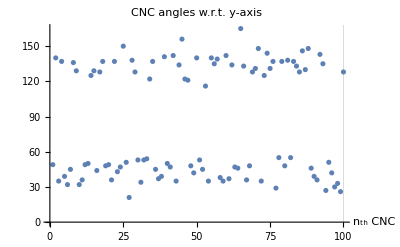
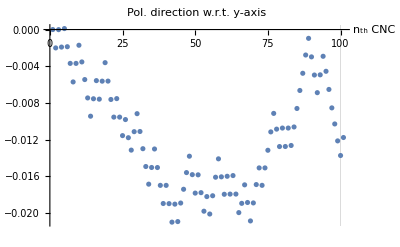
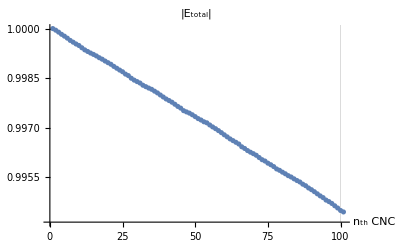
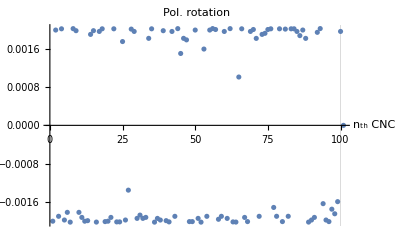

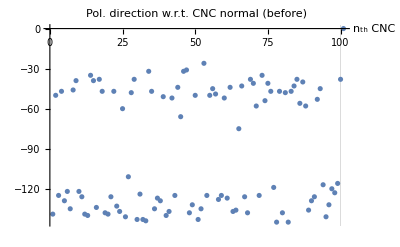
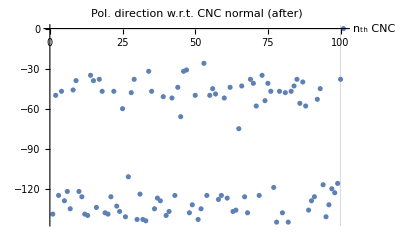

E_total after 100th CNC=0.994458+0. ⅈ

Final intensity after the 2nd polarizer=0.741886+0. ⅈ

```mathematica
{ListPlot[ϕbi180,ImageSize->400,PlotRange->All,AxesLabel->{"n_th CNC",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},GridLines->{{100},{180}},AxesOrigin->{0,0},PlotLabel->"CNC angles w.r.t. y-axis"],
ListPlot[ψy,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. y-axis",GridLines->{{100},None}],
ListPlot[Etot,ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"|E_total|",GridLines->{{100},None}],
ListPlot[(dψ),ImageSize->400,PlotRange->All,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. rotation",GridLines->{{100},None}]}
{ListPlot[ϕbtn,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (before)",GridLines->{{100},None}],
ListPlot[ψres,ImageSize->400,LabelStyle->{FontFamily->"Arial", FontSize->15,Black},AxesLabel->{"n_th CNC",None},PlotLabel->"Pol. direction w.r.t. CNC normal (after)",GridLines->{{100},None}]}

Print["E_total after 100th CNC=",Etot[[n+1]]]
Print["Final intensity after the 2nd polarizer=",PI]
```

#### Check numbers after each CNC

```mathematica
AppendTo[ϕbi180,0];
AppendTo[ϕbi180Norm,0];
ta1=Table[{i,ϕbi180[[i]],ψy[[i]],ϕbi180Norm[[i]],ϕbtn[[i]],ψres[[i]],dψ[[i]],"",ψy[[i]],dψ2[[i]]," ",Etot[[i]],ttot[[i]]},{i,1,n+1}];
PrependTo[ta1,{"nth CNC","CNC ang(180)","ψy","CNC norm ang","Ang btn(ϕbtn)","ψresult (CNC axis)","dψ(after-before)","+CNC norm","ψy","dψ2(ψ_(n + 1)-ψ_n)","-","E_tot","t_tot"}];
ta1//TableForm
```

nth CNC | CNC ang(180) | ψy | CNC norm ang | Ang btn(ϕbtn) | ψresult (CNC axis) | dψ(after-before) | +CNC norm | ψy | dψ2(ψ_(n + 1)-ψ_n) | - | E_tot | t_tot
1 | 49 | 1.×10^-9 | 139 | -139. | -139.002+0. ⅈ | -0.00200072+0. ⅈ |  | 1.×10^-9 | -0.00200072+0. ⅈ |   | 1 | 0.999952+0. ⅈ
2 | 140 | -0.00200072+0. ⅈ | 50 | -50.002+0. ⅈ | -50.+0. ⅈ | 0.00198968+0. ⅈ |  | -0.00200072+0. ⅈ | 0.00198968+0. ⅈ |   | 0.999952+0. ⅈ | 0.999941+0. ⅈ
3 | 35 | -0.0000110335+0. ⅈ | 125 | -125.+0. ⅈ | -125.002+0. ⅈ | -0.00189857+0. ⅈ |  | -0.0000110335+0. ⅈ | -0.00189857+0. ⅈ |   | 0.999892+0. ⅈ | 0.999935+0. ⅈ
4 | 137 | -0.0019096+0. ⅈ | 47 | -47.0019+0. ⅈ | -46.9999+0. ⅈ | 0.00201546+0. ⅈ |  | -0.0019096+0. ⅈ | 0.00201546+0. ⅈ |   | 0.999827+0. ⅈ | 0.999944+0. ⅈ
5 | 39 | 0.000105862+0. ⅈ | 129 | -129.+0. ⅈ | -129.002+0. ⅈ | -0.00197625+0. ⅈ |  | 0.000105862+0. ⅈ | -0.00197625+0. ⅈ |   | 0.999771+0. ⅈ | 0.999939+0. ⅈ
6 | 32 | -0.00187039+0. ⅈ | 122 | -122.002+0. ⅈ | -122.004+0. ⅈ | -0.001816+0. ⅈ |  | -0.00187039+0. ⅈ | -0.001816+0. ⅈ |   | 0.999711+0. ⅈ | 0.999931+0. ⅈ
7 | 45 | -0.00368639+0. ⅈ | 135 | -135.004+0. ⅈ | -135.006+0. ⅈ | -0.00202039+0. ⅈ |  | -0.00368639+0. ⅈ | -0.00202039+0. ⅈ |   | 0.999642+0. ⅈ | 0.999947+0. ⅈ
8 | 136 | -0.00570678+0. ⅈ | 46 | -46.0057+0. ⅈ | -46.0037+0. ⅈ | 0.00201915+0. ⅈ |  | -0.00570678+0. ⅈ | 0.00201915+0. ⅈ |   | 0.999589+0. ⅈ | 0.999946+0. ⅈ
9 | 129 | -0.00368763+0. ⅈ | 39 | -39.0037+0. ⅈ | -39.0017+0. ⅈ | 0.00197628+0. ⅈ |  | -0.00368763+0. ⅈ | 0.00197628+0. ⅈ |   | 0.999534+0. ⅈ | 0.999954+0. ⅈ
10 | 32 | -0.00171135+0. ⅈ | 122 | -122.002+0. ⅈ | -122.004+0. ⅈ | -0.00181599+0. ⅈ |  | -0.00171135+0. ⅈ | -0.00181599+0. ⅈ |   | 0.999489+0. ⅈ | 0.999931+0. ⅈ
11 | 36 | -0.00352735+0. ⅈ | 126 | -126.004+0. ⅈ | -126.005+0. ⅈ | -0.0019216+0. ⅈ |  | -0.00352735+0. ⅈ | -0.0019216+0. ⅈ |   | 0.99942+0. ⅈ | 0.999936+0. ⅈ
12 | 49 | -0.00544895+0. ⅈ | 139 | -139.005+0. ⅈ | -139.007+0. ⅈ | -0.00200066+0. ⅈ |  | -0.00544895+0. ⅈ | -0.00200066+0. ⅈ |   | 0.999356+0. ⅈ | 0.999952+0. ⅈ
13 | 50 | -0.00744961+0. ⅈ | 140 | -140.007+0. ⅈ | -140.009+0. ⅈ | -0.00198959+0. ⅈ |  | -0.00744961+0. ⅈ | -0.00198959+0. ⅈ |   | 0.999308+0. ⅈ | 0.999953+0. ⅈ
14 | 125 | -0.0094392+0. ⅈ | 35 | -35.0094+0. ⅈ | -35.0075+0. ⅈ | 0.00189875+0. ⅈ |  | -0.0094392+0. ⅈ | 0.00189875+0. ⅈ |   | 0.999261+0. ⅈ | 0.999959+0. ⅈ
15 | 129 | -0.00754045+0. ⅈ | 39 | -39.0075+0. ⅈ | -39.0056+0. ⅈ | 0.00197633+0. ⅈ |  | -0.00754045+0. ⅈ | 0.00197633+0. ⅈ |   | 0.999219+0. ⅈ | 0.999954+0. ⅈ
16 | 44 | -0.00556412+0. ⅈ | 134 | -134.006+0. ⅈ | -134.008+0. ⅈ | -0.00201917+0. ⅈ |  | -0.00556412+0. ⅈ | -0.00201917+0. ⅈ |   | 0.999173+0. ⅈ | 0.999946+0. ⅈ
17 | 128 | -0.00758329+0. ⅈ | 38 | -38.0076+0. ⅈ | -38.0056+0. ⅈ | 0.00196049+0. ⅈ |  | -0.00758329+0. ⅈ | 0.00196049+0. ⅈ |   | 0.999119+0. ⅈ | 0.999955+0. ⅈ
18 | 137 | -0.00562281+0. ⅈ | 47 | -47.0056+0. ⅈ | -47.0036+0. ⅈ | 0.00201544+0. ⅈ |  | -0.00562281+0. ⅈ | 0.00201544+0. ⅈ |   | 0.999074+0. ⅈ | 0.999944+0. ⅈ
19 | 48 | -0.00360736+0. ⅈ | 138 | -138.004+0. ⅈ | -138.006+0. ⅈ | -0.00200929+0. ⅈ |  | -0.00360736+0. ⅈ | -0.00200929+0. ⅈ |   | 0.999019+0. ⅈ | 0.99995+0. ⅈ
20 | 49 | -0.00561665+0. ⅈ | 139 | -139.006+0. ⅈ | -139.008+0. ⅈ | -0.00200066+0. ⅈ |  | -0.00561665+0. ⅈ | -0.00200066+0. ⅈ |   | 0.998969+0. ⅈ | 0.999952+0. ⅈ
21 | 36 | -0.00761731+0. ⅈ | 126 | -126.008+0. ⅈ | -126.01+0. ⅈ | -0.00192169+0. ⅈ |  | -0.00761731+0. ⅈ | -0.00192169+0. ⅈ |   | 0.998921+0. ⅈ | 0.999936+0. ⅈ
22 | 137 | -0.009539+0. ⅈ | 47 | -47.0095+0. ⅈ | -47.0075+0. ⅈ | 0.00201542+0. ⅈ |  | -0.009539+0. ⅈ | 0.00201542+0. ⅈ |   | 0.998857+0. ⅈ | 0.999944+0. ⅈ
23 | 43 | -0.00752357+0. ⅈ | 133 | -133.008+0. ⅈ | -133.01+0. ⅈ | -0.00201551+0. ⅈ |  | -0.00752357+0. ⅈ | -0.00201551+0. ⅈ |   | 0.998801+0. ⅈ | 0.999944+0. ⅈ
24 | 47 | -0.00953908+0. ⅈ | 137 | -137.01+0. ⅈ | -137.012+0. ⅈ | -0.00201541+0. ⅈ |  | -0.00953908+0. ⅈ | -0.00201541+0. ⅈ |   | 0.998746+0. ⅈ | 0.999949+0. ⅈ
25 | 150 | -0.0115545+0. ⅈ | 60 | -60.0116+0. ⅈ | -60.0098+0. ⅈ | 0.00174933+0. ⅈ |  | -0.0115545+0. ⅈ | 0.00174933+0. ⅈ |   | 0.998695+0. ⅈ | 0.999929+0. ⅈ
26 | 51 | -0.00980517+0. ⅈ | 141 | -141.01+0. ⅈ | -141.012+0. ⅈ | -0.00197608+0. ⅈ |  | -0.00980517+0. ⅈ | -0.00197608+0. ⅈ |   | 0.998624+0. ⅈ | 0.999954+0. ⅈ
27 | 21 | -0.0117812+0. ⅈ | 111 | -111.012+0. ⅈ | -111.013+0. ⅈ | -0.00135256+0. ⅈ |  | -0.0117812+0. ⅈ | -0.00135256+0. ⅈ |   | 0.998578+0. ⅈ | 0.999921+0. ⅈ
28 | 138 | -0.0131338+0. ⅈ | 48 | -48.0131+0. ⅈ | -48.0111+0. ⅈ | 0.00200923+0. ⅈ |  | -0.0131338+0. ⅈ | 0.00200923+0. ⅈ |   | 0.998499+0. ⅈ | 0.999943+0. ⅈ
29 | 128 | -0.0111246+0. ⅈ | 38 | -38.0111+0. ⅈ | -38.0092+0. ⅈ | 0.00196055+0. ⅈ |  | -0.0111246+0. ⅈ | 0.00196055+0. ⅈ |   | 0.998442+0. ⅈ | 0.999955+0. ⅈ
30 | 53 | -0.00916403+0. ⅈ | 143 | -143.009+0. ⅈ | -143.011+0. ⅈ | -0.00194192+0. ⅈ |  | -0.00916403+0. ⅈ | -0.00194192+0. ⅈ |   | 0.998398+0. ⅈ | 0.999956+0. ⅈ
31 | 34 | -0.0111059+0. ⅈ | 124 | -124.011+0. ⅈ | -124.013+0. ⅈ | -0.00187359+0. ⅈ |  | -0.0111059+0. ⅈ | -0.00187359+0. ⅈ |   | 0.998354+0. ⅈ | 0.999934+0. ⅈ
32 | 53 | -0.0129795+0. ⅈ | 143 | -143.013+0. ⅈ | -143.015+0. ⅈ | -0.00194185+0. ⅈ |  | -0.0129795+0. ⅈ | -0.00194185+0. ⅈ |   | 0.998288+0. ⅈ | 0.999957+0. ⅈ
33 | 54 | -0.0149214+0. ⅈ | 144 | -144.015+0. ⅈ | -144.017+0. ⅈ | -0.00192116+0. ⅈ |  | -0.0149214+0. ⅈ | -0.00192116+0. ⅈ |   | 0.998244+0. ⅈ | 0.999958+0. ⅈ
34 | 122 | -0.0168425+0. ⅈ | 32 | -32.0168+0. ⅈ | -32.015+0. ⅈ | 0.00181641+0. ⅈ |  | -0.0168425+0. ⅈ | 0.00181641+0. ⅈ |   | 0.998202+0. ⅈ | 0.999962+0. ⅈ
35 | 137 | -0.0150261+0. ⅈ | 47 | -47.015+0. ⅈ | -47.013+0. ⅈ | 0.0020154+0. ⅈ |  | -0.0150261+0. ⅈ | 0.0020154+0. ⅈ |   | 0.998164+0. ⅈ | 0.999944+0. ⅈ
36 | 45 | -0.0130107+0. ⅈ | 135 | -135.013+0. ⅈ | -135.015+0. ⅈ | -0.00202039+0. ⅈ |  | -0.0130107+0. ⅈ | -0.00202039+0. ⅈ |   | 0.998109+0. ⅈ | 0.999947+0. ⅈ
37 | 37 | -0.0150311+0. ⅈ | 127 | -127.015+0. ⅈ | -127.017+0. ⅈ | -0.00194243+0. ⅈ |  | -0.0150311+0. ⅈ | -0.00194243+0. ⅈ |   | 0.998056+0. ⅈ | 0.999937+0. ⅈ
38 | 39 | -0.0169736+0. ⅈ | 129 | -129.017+0. ⅈ | -129.019+0. ⅈ | -0.0019765+0. ⅈ |  | -0.0169736+0. ⅈ | -0.0019765+0. ⅈ |   | 0.997993+0. ⅈ | 0.999939+0. ⅈ
39 | 141 | -0.0189501+0. ⅈ | 51 | -51.019+0. ⅈ | -51.017+0. ⅈ | 0.00197597+0. ⅈ |  | -0.0189501+0. ⅈ | 0.00197597+0. ⅈ |   | 0.997933+0. ⅈ | 0.999939+0. ⅈ
40 | 50 | -0.0169741+0. ⅈ | 140 | -140.017+0. ⅈ | -140.019+0. ⅈ | -0.00198947+0. ⅈ |  | -0.0169741+0. ⅈ | -0.00198947+0. ⅈ |   | 0.997872+0. ⅈ | 0.999953+0. ⅈ
41 | 47 | -0.0189636+0. ⅈ | 137 | -137.019+0. ⅈ | -137.021+0. ⅈ | -0.00201537+0. ⅈ |  | -0.0189636+0. ⅈ | -0.00201537+0. ⅈ |   | 0.997825+0. ⅈ | 0.999949+0. ⅈ
42 | 142 | -0.0209789+0. ⅈ | 52 | -52.021+0. ⅈ | -52.019+0. ⅈ | 0.00196003+0. ⅈ |  | -0.0209789+0. ⅈ | 0.00196003+0. ⅈ |   | 0.997774+0. ⅈ | 0.999938+0. ⅈ
43 | 35 | -0.0190189+0. ⅈ | 125 | -125.019+0. ⅈ | -125.021+0. ⅈ | -0.00189903+0. ⅈ |  | -0.0190189+0. ⅈ | -0.00189903+0. ⅈ |   | 0.997713+0. ⅈ | 0.999935+0. ⅈ
44 | 134 | -0.0209179+0. ⅈ | 44 | -44.0209+0. ⅈ | -44.0189+0. ⅈ | 0.00201921+0. ⅈ |  | -0.0209179+0. ⅈ | 0.00201921+0. ⅈ |   | 0.997648+0. ⅈ | 0.999948+0. ⅈ
45 | 156 | -0.0188987+0. ⅈ | 66 | -66.0189+0. ⅈ | -66.0174+0. ⅈ | 0.00150058+0. ⅈ |  | -0.0188987+0. ⅈ | 0.00150058+0. ⅈ |   | 0.997596+0. ⅈ | 0.999923+0. ⅈ
46 | 122 | -0.0173981+0. ⅈ | 32 | -32.0174+0. ⅈ | -32.0156+0. ⅈ | 0.00181642+0. ⅈ |  | -0.0173981+0. ⅈ | 0.00181642+0. ⅈ |   | 0.997519+0. ⅈ | 0.999962+0. ⅈ
47 | 121 | -0.0155817+0. ⅈ | 31 | -31.0156+0. ⅈ | -31.0138+0. ⅈ | 0.00178438+0. ⅈ |  | -0.0155817+0. ⅈ | 0.00178438+0. ⅈ |   | 0.997481+0. ⅈ | 0.999963+0. ⅈ
48 | 48 | -0.0137973+0. ⅈ | 138 | -138.014+0. ⅈ | -138.016+0. ⅈ | -0.00200921+0. ⅈ |  | -0.0137973+0. ⅈ | -0.00200921+0. ⅈ |   | 0.997445+0. ⅈ | 0.99995+0. ⅈ
49 | 42 | -0.0158065+0. ⅈ | 132 | -132.016+0. ⅈ | -132.018+0. ⅈ | -0.00200944+0. ⅈ |  | -0.0158065+0. ⅈ | -0.00200944+0. ⅈ |   | 0.997395+0. ⅈ | 0.999943+0. ⅈ
50 | 140 | -0.017816+0. ⅈ | 50 | -50.0178+0. ⅈ | -50.0158+0. ⅈ | 0.00198949+0. ⅈ |  | -0.017816+0. ⅈ | 0.00198949+0. ⅈ |   | 0.997339+0. ⅈ | 0.999941+0. ⅈ
51 | 53 | -0.0158265+0. ⅈ | 143 | -143.016+0. ⅈ | -143.018+0. ⅈ | -0.0019418+0. ⅈ |  | -0.0158265+0. ⅈ | -0.0019418+0. ⅈ |   | 0.997279+0. ⅈ | 0.999957+0. ⅈ
52 | 45 | -0.0177683+0. ⅈ | 135 | -135.018+0. ⅈ | -135.02+0. ⅈ | -0.00202039+0. ⅈ |  | -0.0177683+0. ⅈ | -0.00202039+0. ⅈ |   | 0.997236+0. ⅈ | 0.999947+0. ⅈ
53 | 116 | -0.0197887+0. ⅈ | 26 | -26.0198+0. ⅈ | -26.0182+0. ⅈ | 0.00159291+0. ⅈ |  | -0.0197887+0. ⅈ | 0.00159291+0. ⅈ |   | 0.997183+0. ⅈ | 0.999968+0. ⅈ
54 | 35 | -0.0181958+0. ⅈ | 125 | -125.018+0. ⅈ | -125.02+0. ⅈ | -0.00189901+0. ⅈ |  | -0.0181958+0. ⅈ | -0.00189901+0. ⅈ |   | 0.997152+0. ⅈ | 0.999935+0. ⅈ
55 | 140 | -0.0200948+0. ⅈ | 50 | -50.0201+0. ⅈ | -50.0181+0. ⅈ | 0.00198946+0. ⅈ |  | -0.0200948+0. ⅈ | 0.00198946+0. ⅈ |   | 0.997086+0. ⅈ | 0.999941+0. ⅈ
56 | 135 | -0.0181053+0. ⅈ | 45 | -45.0181+0. ⅈ | -45.0161+0. ⅈ | 0.00202039+0. ⅈ |  | -0.0181053+0. ⅈ | 0.00202039+0. ⅈ |   | 0.997027+0. ⅈ | 0.999947+0. ⅈ
57 | 139 | -0.0160849+0. ⅈ | 49 | -49.0161+0. ⅈ | -49.0141+0. ⅈ | 0.00200058+0. ⅈ |  | -0.0160849+0. ⅈ | 0.00200058+0. ⅈ |   | 0.996974+0. ⅈ | 0.999942+0. ⅈ
58 | 38 | -0.0140843+0. ⅈ | 128 | -128.014+0. ⅈ | -128.016+0. ⅈ | -0.00196063+0. ⅈ |  | -0.0140843+0. ⅈ | -0.00196063+0. ⅈ |   | 0.996916+0. ⅈ | 0.999938+0. ⅈ
59 | 35 | -0.016045+0. ⅈ | 125 | -125.016+0. ⅈ | -125.018+0. ⅈ | -0.00189895+0. ⅈ |  | -0.016045+0. ⅈ | -0.00189895+0. ⅈ |   | 0.996855+0. ⅈ | 0.999935+0. ⅈ
60 | 142 | -0.0179439+0. ⅈ | 52 | -52.0179+0. ⅈ | -52.016+0. ⅈ | 0.00196008+0. ⅈ |  | -0.0179439+0. ⅈ | 0.00196008+0. ⅈ |   | 0.99679+0. ⅈ | 0.999938+0. ⅈ
61 | 37 | -0.0159838+0. ⅈ | 127 | -127.016+0. ⅈ | -127.018+0. ⅈ | -0.00194245+0. ⅈ |  | -0.0159838+0. ⅈ | -0.00194245+0. ⅈ |   | 0.996728+0. ⅈ | 0.999937+0. ⅈ
62 | 134 | -0.0179263+0. ⅈ | 44 | -44.0179+0. ⅈ | -44.0159+0. ⅈ | 0.0020192+0. ⅈ |  | -0.0179263+0. ⅈ | 0.0020192+0. ⅈ |   | 0.996665+0. ⅈ | 0.999948+0. ⅈ
63 | 47 | -0.0159071+0. ⅈ | 137 | -137.016+0. ⅈ | -137.018+0. ⅈ | -0.00201538+0. ⅈ |  | -0.0159071+0. ⅈ | -0.00201538+0. ⅈ |   | 0.996613+0. ⅈ | 0.999949+0. ⅈ
64 | 46 | -0.0179225+0. ⅈ | 136 | -136.018+0. ⅈ | -136.02+0. ⅈ | -0.00201911+0. ⅈ |  | -0.0179225+0. ⅈ | -0.00201911+0. ⅈ |   | 0.996563+0. ⅈ | 0.999948+0. ⅈ
65 | 165 | -0.0199416+0. ⅈ | 75 | -75.0199+0. ⅈ | -75.0189+0. ⅈ | 0.00100901+0. ⅈ |  | -0.0199416+0. ⅈ | 0.00100901+0. ⅈ |   | 0.996511+0. ⅈ | 0.999916+0. ⅈ
66 | 133 | -0.0189326+0. ⅈ | 43 | -43.0189+0. ⅈ | -43.0169+0. ⅈ | 0.00201555+0. ⅈ |  | -0.0189326+0. ⅈ | 0.00201555+0. ⅈ |   | 0.996428+0. ⅈ | 0.999949+0. ⅈ
67 | 36 | -0.016917+0. ⅈ | 126 | -126.017+0. ⅈ | -126.019+0. ⅈ | -0.00192189+0. ⅈ |  | -0.016917+0. ⅈ | -0.00192189+0. ⅈ |   | 0.996377+0. ⅈ | 0.999936+0. ⅈ
68 | 48 | -0.0188389+0. ⅈ | 138 | -138.019+0. ⅈ | -138.021+0. ⅈ | -0.00200917+0. ⅈ |  | -0.0188389+0. ⅈ | -0.00200917+0. ⅈ |   | 0.996313+0. ⅈ | 0.99995+0. ⅈ
69 | 128 | -0.0208481+0. ⅈ | 38 | -38.0208+0. ⅈ | -38.0189+0. ⅈ | 0.00196071+0. ⅈ |  | -0.0208481+0. ⅈ | 0.00196071+0. ⅈ |   | 0.996264+0. ⅈ | 0.999955+0. ⅈ
70 | 131 | -0.0188874+0. ⅈ | 41 | -41.0189+0. ⅈ | -41.0169+0. ⅈ | 0.0020009+0. ⅈ |  | -0.0188874+0. ⅈ | 0.0020009+0. ⅈ |   | 0.996219+0. ⅈ | 0.999952+0. ⅈ
71 | 148 | -0.0168865+0. ⅈ | 58 | -58.0169+0. ⅈ | -58.0151+0. ⅈ | 0.00181542+0. ⅈ |  | -0.0168865+0. ⅈ | 0.00181542+0. ⅈ |   | 0.996171+0. ⅈ | 0.999931+0. ⅈ
72 | 35 | -0.0150711+0. ⅈ | 125 | -125.015+0. ⅈ | -125.017+0. ⅈ | -0.00189893+0. ⅈ |  | -0.0150711+0. ⅈ | -0.00189893+0. ⅈ |   | 0.996103+0. ⅈ | 0.999935+0. ⅈ
73 | 125 | -0.01697+0. ⅈ | 35 | -35.017+0. ⅈ | -35.0151+0. ⅈ | 0.00189893+0. ⅈ |  | -0.01697+0. ⅈ | 0.00189893+0. ⅈ |   | 0.996038+0. ⅈ | 0.999959+0. ⅈ
74 | 144 | -0.0150711+0. ⅈ | 54 | -54.0151+0. ⅈ | -54.0131+0. ⅈ | 0.0019212+0. ⅈ |  | -0.0150711+0. ⅈ | 0.0019212+0. ⅈ |   | 0.995996+0. ⅈ | 0.999936+0. ⅈ
75 | 131 | -0.0131499+0. ⅈ | 41 | -41.0131+0. ⅈ | -41.0111+0. ⅈ | 0.00200085+0. ⅈ |  | -0.0131499+0. ⅈ | 0.00200085+0. ⅈ |   | 0.995933+0. ⅈ | 0.999952+0. ⅈ
76 | 137 | -0.011149+0. ⅈ | 47 | -47.0111+0. ⅈ | -47.0091+0. ⅈ | 0.00201542+0. ⅈ |  | -0.011149+0. ⅈ | 0.00201542+0. ⅈ |   | 0.995884+0. ⅈ | 0.999944+0. ⅈ
77 | 29 | -0.00913361+0. ⅈ | 119 | -119.009+0. ⅈ | -119.011+0. ⅈ | -0.00171376+0. ⅈ |  | -0.00913361+0. ⅈ | -0.00171376+0. ⅈ |   | 0.995829+0. ⅈ | 0.999928+0. ⅈ
78 | 55 | -0.0108474+0. ⅈ | 145 | -145.011+0. ⅈ | -145.013+0. ⅈ | -0.00189826+0. ⅈ |  | -0.0108474+0. ⅈ | -0.00189826+0. ⅈ |   | 0.995757+0. ⅈ | 0.999959+0. ⅈ
79 | 137 | -0.0127456+0. ⅈ | 47 | -47.0127+0. ⅈ | -47.0107+0. ⅈ | 0.00201541+0. ⅈ |  | -0.0127456+0. ⅈ | 0.00201541+0. ⅈ |   | 0.995716+0. ⅈ | 0.999944+0. ⅈ
80 | 48 | -0.0107302+0. ⅈ | 138 | -138.011+0. ⅈ | -138.013+0. ⅈ | -0.00200923+0. ⅈ |  | -0.0107302+0. ⅈ | -0.00200923+0. ⅈ |   | 0.995661+0. ⅈ | 0.99995+0. ⅈ
81 | 138 | -0.0127395+0. ⅈ | 48 | -48.0127+0. ⅈ | -48.0107+0. ⅈ | 0.00200923+0. ⅈ |  | -0.0127395+0. ⅈ | 0.00200923+0. ⅈ |   | 0.995612+0. ⅈ | 0.999943+0. ⅈ
82 | 55 | -0.0107302+0. ⅈ | 145 | -145.011+0. ⅈ | -145.013+0. ⅈ | -0.00189826+0. ⅈ |  | -0.0107302+0. ⅈ | -0.00189826+0. ⅈ |   | 0.995555+0. ⅈ | 0.999959+0. ⅈ
83 | 137 | -0.0126285+0. ⅈ | 47 | -47.0126+0. ⅈ | -47.0106+0. ⅈ | 0.00201541+0. ⅈ |  | -0.0126285+0. ⅈ | 0.00201541+0. ⅈ |   | 0.995514+0. ⅈ | 0.999944+0. ⅈ
84 | 133 | -0.0106131+0. ⅈ | 43 | -43.0106+0. ⅈ | -43.0086+0. ⅈ | 0.00201551+0. ⅈ |  | -0.0106131+0. ⅈ | 0.00201551+0. ⅈ |   | 0.995459+0. ⅈ | 0.999949+0. ⅈ
85 | 128 | -0.00859756+0. ⅈ | 38 | -38.0086+0. ⅈ | -38.0066+0. ⅈ | 0.0019605+0. ⅈ |  | -0.00859756+0. ⅈ | 0.0019605+0. ⅈ |   | 0.995408+0. ⅈ | 0.999955+0. ⅈ
86 | 146 | -0.00663705+0. ⅈ | 56 | -56.0066+0. ⅈ | -56.0048+0. ⅈ | 0.00187312+0. ⅈ |  | -0.00663705+0. ⅈ | 0.00187312+0. ⅈ |   | 0.995363+0. ⅈ | 0.999934+0. ⅈ
87 | 130 | -0.00476393+0. ⅈ | 40 | -40.0048+0. ⅈ | -40.0028+0. ⅈ | 0.00198974+0. ⅈ |  | -0.00476393+0. ⅈ | 0.00198974+0. ⅈ |   | 0.995297+0. ⅈ | 0.999953+0. ⅈ
88 | 148 | -0.00277419+0. ⅈ | 58 | -58.0028+0. ⅈ | -58.001+0. ⅈ | 0.00181586+0. ⅈ |  | -0.00277419+0. ⅈ | 0.00181586+0. ⅈ |   | 0.99525+0. ⅈ | 0.999931+0. ⅈ
89 | 46 | -0.000958338+0. ⅈ | 136 | -136.001+0. ⅈ | -136.003+0. ⅈ | -0.00201915+0. ⅈ |  | -0.000958338+0. ⅈ | -0.00201915+0. ⅈ |   | 0.995182+0. ⅈ | 0.999948+0. ⅈ
90 | 39 | -0.00297749+0. ⅈ | 129 | -129.003+0. ⅈ | -129.005+0. ⅈ | -0.0019763+0. ⅈ |  | -0.00297749+0. ⅈ | -0.0019763+0. ⅈ |   | 0.99513+0. ⅈ | 0.999939+0. ⅈ
91 | 36 | -0.00495379+0. ⅈ | 126 | -126.005+0. ⅈ | -126.007+0. ⅈ | -0.00192163+0. ⅈ |  | -0.00495379+0. ⅈ | -0.00192163+0. ⅈ |   | 0.99507+0. ⅈ | 0.999936+0. ⅈ
92 | 143 | -0.00687542+0. ⅈ | 53 | -53.0069+0. ⅈ | -53.0049+0. ⅈ | 0.00194201+0. ⅈ |  | -0.00687542+0. ⅈ | 0.00194201+0. ⅈ |   | 0.995006+0. ⅈ | 0.999937+0. ⅈ
93 | 135 | -0.00493341+0. ⅈ | 45 | -45.0049+0. ⅈ | -45.0029+0. ⅈ | 0.00202039+0. ⅈ |  | -0.00493341+0. ⅈ | 0.00202039+0. ⅈ |   | 0.994944+0. ⅈ | 0.999947+0. ⅈ
94 | 27 | -0.00291302+0. ⅈ | 117 | -117.003+0. ⅈ | -117.005+0. ⅈ | -0.00163468+0. ⅈ |  | -0.00291302+0. ⅈ | -0.00163468+0. ⅈ |   | 0.994891+0. ⅈ | 0.999926+0. ⅈ
95 | 51 | -0.00454771+0. ⅈ | 141 | -141.005+0. ⅈ | -141.007+0. ⅈ | -0.00197616+0. ⅈ |  | -0.00454771+0. ⅈ | -0.00197616+0. ⅈ |   | 0.994817+0. ⅈ | 0.999954+0. ⅈ
96 | 42 | -0.00652386+0. ⅈ | 132 | -132.007+0. ⅈ | -132.009+0. ⅈ | -0.00200938+0. ⅈ |  | -0.00652386+0. ⅈ | -0.00200938+0. ⅈ |   | 0.994771+0. ⅈ | 0.999943+0. ⅈ
97 | 30 | -0.00853324+0. ⅈ | 120 | -120.009+0. ⅈ | -120.01+0. ⅈ | -0.00175004+0. ⅈ |  | -0.00853324+0. ⅈ | -0.00175004+0. ⅈ |   | 0.994715+0. ⅈ | 0.999929+0. ⅈ
98 | 33 | -0.0102833+0. ⅈ | 123 | -123.01+0. ⅈ | -123.012+0. ⅈ | -0.00184604+0. ⅈ |  | -0.0102833+0. ⅈ | -0.00184604+0. ⅈ |   | 0.994644+0. ⅈ | 0.999932+0. ⅈ
99 | 26 | -0.0121293+0. ⅈ | 116 | -116.012+0. ⅈ | -116.014+0. ⅈ | -0.00159265+0. ⅈ |  | -0.0121293+0. ⅈ | -0.00159265+0. ⅈ |   | 0.994577+0. ⅈ | 0.999925+0. ⅈ
100 | 128 | -0.013722+0. ⅈ | 38 | -38.0137+0. ⅈ | -38.0118+0. ⅈ | 0.00196059+0. ⅈ |  | -0.013722+0. ⅈ | 0.00196059+0. ⅈ |   | 0.994503+0. ⅈ | 0.999955+0. ⅈ
101 | 0 | -0.0117614+0. ⅈ | 0 | 0 | 0 | 0 |  | -0.0117614+0. ⅈ | 0 |   | 0.994458+0. ⅈ | 0

## G. Final intensity as a function of the incident polarization angle Note: the same calculation with various incident polarization angle (no explanation included). Data exportation included.

#### Loop

```mathematica
(*Crossed-polylamellate*)
PIcl[x_]:=Module[{},
ϕi=x+ϵ;(* Polarization direction w.r.t. y-axis *)
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

(**)
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕcl180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕcl180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)

];
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕi)*π/180])^2
]
clAng=Table[{i,PIcl[i]},{i,0,180,5}];
```

```mathematica
(*Random*)
PIra[x_]:=Module[{},
ϕi=x+ϵ;(* Polarization direction w.r.t. y-axis *)
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

(**)
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕra180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕra180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)

];
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕi)*π/180])^2
]
raAng=Table[{i,PIra[i]},{i,0,180,5}];
```

```mathematica
(*Helicoidal*)
PIhe[x_]:=Module[{},
ϕi=x+ϵ;(* Polarization direction w.r.t. y-axis *)
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

(**)
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕhe180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕhe180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)

];
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕi)*π/180])^2
]
heAng=Table[{i,PIhe[i]},{i,0,180,5}];
```

```mathematica
(*Uniaxial*)
PIun[x_]:=Module[{},
ϕi=x+ϵ;(* Polarization direction w.r.t. y-axis *)
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

(**)
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕun180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕun180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)

];
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕi)*π/180])^2
]
unAng=Table[{i,PIun[i]},{i,0,180,5}];
```

```mathematica
(*Bimodal*)
PIbi[x_]:=Module[{},
ϕi=x+ϵ;(* Polarization direction w.r.t. y-axis *)
ψy=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)
ψy[[1]]=N[ϕi];

ϕbtn=Table[0,{i,1,n+1}]; (*angle between Pol. direction & CNC normal*)

ψres=Table[0,{i,1,n+1}]; (* Azimuth angle after passing a CNC*)

Etot=Table[0,{i,1,n+1}];
Etot[[1]]=1;
ttot=Table[0,{i,1,n+1}];

dψ=Table[0,{i,1,n+1}];
dψ2=Table[0,{i,1,n+1}];

(**)
For[p=1,p<n+1,p++,

ϕbtn[[p]]=ψy[[p]]-ϕbi180Norm[[p]]; (* convert axis: From y-axis to CNC normal *)
ψres[[p]]=ψ[ϕbtn[[p]]]; (* result of rotation in CNC normal axis*)
ψy[[p+1]]=ψres[[p]]+ϕbi180Norm[[p]]; (* back to y-axis system*) (*F180 is for *) 

dψ[[p]]=ψres[[p]]-ϕbtn[[p]]; (* (ψafter - ψbefore) in CNC axis *)

ttot[[p]]=tt[ϕbtn[[p]]];
Etot[[p+1]]=Etot[[p]]*ttot[[p]]; (* energy loss as passing through *)

dψ2[[p]]=ψy[[p+1]]-ψy[[p]]; (* (ψafter - ψbefore) in CNC axis. How much rotation @ each CNC*)

];
PI=(Etot[[n+1]]*Sin[(ψy[[n+1]]-ϕi)*π/180])^2
]
biAng=Table[{i,PIbi[i]},{i,0,180,5}];
```

#### Plot check

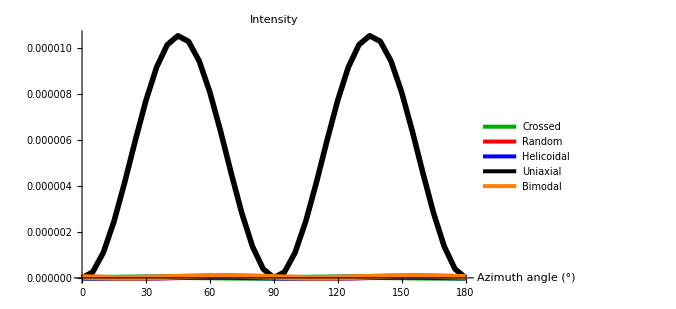
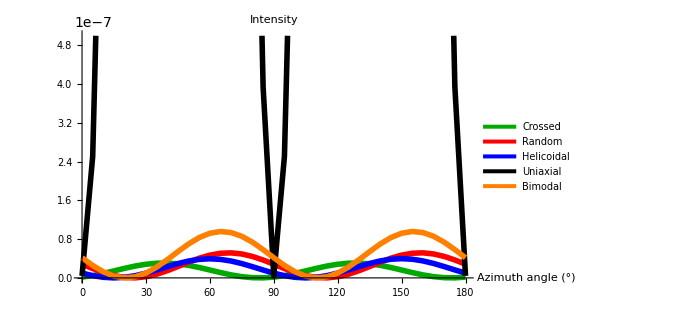

```mathematica
(* Check plots *)
{ListPlot[{clAng,raAng,heAng,unAng,biAng},PlotStyle->{{Darker[Green],Thickness[0.008]},{Red,Thickness[0.008]},{Blue,Thickness[0.008]},{Black,Thickness[0.008]},{Orange,Thickness[0.008]}},Ticks->{Table[30i,{i,0,6}],Automatic},PlotRange->All,ImageSize->500,AxesLabel->{"  Azimuth angle (°)",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},PlotLabel->Style["Intensity",20,Black,Bold],Joined->True,PlotLegends->{"Crossed","Random","Helicoidal","Uniaxial","Bimodal"}],
ListPlot[{clAng,raAng,heAng,unAng,biAng},PlotStyle->{{Darker[Green],Thickness[0.008]},{Red,Thickness[0.008]},{Blue,Thickness[0.008]},{Black,Thickness[0.008]},{Orange,Thickness[0.008]}},Ticks->{Table[30i,{i,0,6}],Automatic},PlotRange->{All,{0,5*10^-7}},ImageSize->500,AxesLabel->{"  Azimuth angle (°)",None},LabelStyle->{FontFamily->"Arial", FontSize->15,Black},PlotLabel->Style["Intensity",20,Black,Bold],Joined->True,PlotLegends->{"Crossed","Random","Helicoidal","Uniaxial","Bimodal"}]}
```

## H. Data export

```mathematica
(* Combine generated data *)
clAng2=Transpose[clAng];
raAng2=Transpose[raAng];
heAng2=Transpose[heAng];
unAng2=Transpose[unAng];
biAng2=Transpose[biAng];
b1={clAng2[[1]],clAng2[[2]],raAng2[[2]],heAng2[[2]],unAng2[[2]],biAng2[[2]]};
b1=Abs[b1];
b1=b1//Transpose;
b1//MatrixForm;
b1=PrependTo[b1,{"wavenumber","crossed-polylamellate","random","helicoidal10","uniaxial","bimodal"}];

(* Data exportation *)
name=CurrentValue[EvaluationNotebook[],{"NotebookFileName"}];
name=StringDrop[name,-3];
time=TextString[TimeObject[]];
time2=ToExpression["StringTake[time,2]"]<>ToString["."]<>ToExpression["StringTake[time,{4,5}]"]<>ToString["."]<>ToExpression["StringTake[time,-2]"]
Export[NotebookDirectory[]<>ToExpression["name"]<>ToExpression["time2"]<>ToString["_"]<>"CRHUB.xlsx",b1];
```

15.18.50